# Hardware Verification Workflow with SCR1

## Что мы сделали?

Мы написали драйвер для SCR1 с помощью Device  Framework

SCR1 — это:
 - Open-source microcontroller core
 - RISC-V architecture (RV32I|E[MC])
 github.com/syntacore/scr1
 
 RISCV — открытая компьютерная архитектура 
 riscv.org

#### Структура SCR1

Зачем это надо?

Как с этим работать?

#### Инициализация

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SCR1Device`"];
```

#### Подключаемся к устройству

```mathematica
device = DeviceOpen["SCR1"]
```

DeviceObject[…]

#### Мы можем отключится от устройства

```mathematica
DeviceClose[device]
```

#### Выполнить RESET устройства, загрузить программу в память процессора

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}]
```

0

#### Мы можем шагать процессорам от инструкции к инструкции

```mathematica
DeviceRead[device,"next_ipc"]
```

520

#### Граф выполнения программы

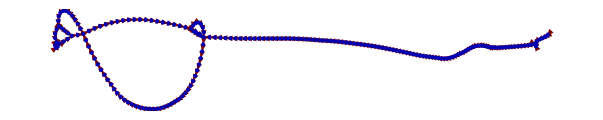

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
ipcList = Table[DeviceRead[device,"next_ipc"],10000];g=Union[BlockMap[#[[1]]->#[[2]]&,ipcList,2,1]];
GraphPlot[g,DirectedEdges-> True]
```

#### Мы можем получить содержимое регистров

```mathematica
Dataset[
Table[
{
i,
BaseForm[DeviceRead[device,{"get_reg",i}],16],
BaseForm[DeviceRead[device,{"get_reg",i}],2]
},
{i,1,31}
]
]
```

Dataset[<>]

#### Мы можем отследить изменение регистров

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
Table[DeviceRead[device,"next_ipc"],12000];
ListAnimate[Table[DeviceRead[device,"next_ipc"];MatrixPlot[BlockMap[#&,Map[#[[2]]&,Table[{i,DeviceRead[device,{"get_reg",i}]},{i,1,31}]],6],ColorFunction->"SunsetColors"],
1000
]]
```

#### Мы можем читать память

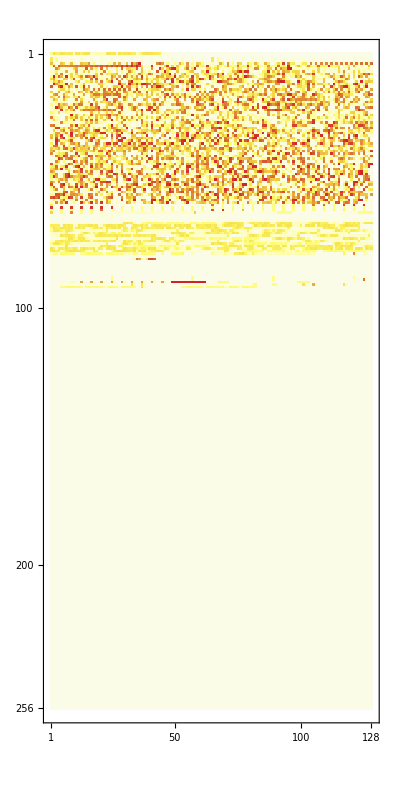

```mathematica
MatrixPlot[
BlockMap[#&,Map[#&,DeviceRead[device,{"read_mem",0,32*1024}]],128],
ColorFunction->"TemperatureMap"
]
```

#### Мы можем оценить статистику доступа к памяти

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
busData=Table[
DeviceRead[device,"step"];
DeviceRead[device,"get_data_bus"
],100000];
```

```mathematica
busDataClean=Select[busData,#[[1]]>0 &];
```

```mathematica
busDataCleanFull=Flatten[Map[
Range[
#[[1]],#[[1]]+(#[[2]]-1)
]&,
busDataClean]];
```

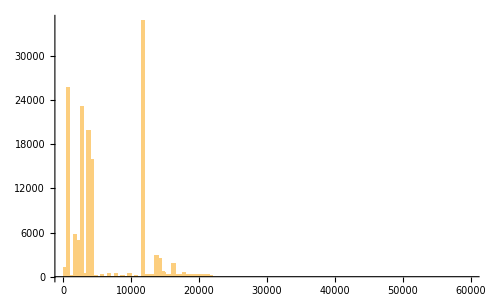

```mathematica
Histogram[busDataCleanFull,{0,60000,500}]
```

#### Мы можем проектировать новые устройства

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/dhrystone.bin"
}];
```

```mathematica
branchstatelist=Table[
DeviceRead[device,"next_ipc"];
DeviceRead[device,"get_branch_state"],
20000
];
```

```mathematica
jumpsDataset=Select[branchstatelist,(#[[3]]+#[[4]]>0)&];
```

```mathematica
jumpsDataset//TableView
```

1:eJzt2rFLVVEcB/BbTysV1CE0RKTiIRHODeLQECEhEg4N0RQF0VDQ0CDh0CQN
IQ2N0iwhDU7NEeEQDQ0NESHR1F/QEJ3T7aLnh8KDwh72ufB4/D6c873Xy9eH
7+Kp63cX7hyuqurmcFX1pvexPKTjUP32a2aMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYYY4wxxhhjjDHGGGOMMcYY
Y4wxxhhjjDHGGGOMMcYYO8jW/m2NZ1vsK9flebVVrltP87NgW2k+2Sr35rkd
1k236tdOm2ptn6PZm+etYFutzq9lJFi+lolg7T3OK0+ePHny5MmTJ0+ePHny
5DV5nX7XnQrrphhj/9z24xnUfjwPmxssLc+dXl+3f8bKkydPnjx58uTJkydP
njzPtBj7n+2gPL/q9Fq6/bNTnjx58g5a3nqwnPch2OyRqlo5Up43z5O9peX5
3Fi5txqvqvPBvqX5YrBPab48Vubl+VZY9yDNa2Fdnt8Hy/NMb7l3vqd+7VyX
548j5bqtE1X1NdjqaLruYCvJ+kdLm0jzldHyHHleDpbnbrpXS+G+5Hkx2KJ7
tee9ethT5uV79SSsy/OrYHnu9Hd1I+zd6LK8t+Ee5Dx//8mTJ0+ePHl/L8+z
XMa6z/7kWem7vnLv8mD67j1U2o00Xwp2O82Pg10drqrnwe4nexFsPNnrYPeS
be6y7nOwpWRfdln3PdijZD92WXd8uLSnw7UXlvadCTaT5ulgc2m+NrQ95yPP
C0fDfUlz+1i5Ls+b4f8s87zWX+6dTXY6/ByTaX7ZX+7N85uw9+xA53vz2p2W
5wsD5d75NE+FvXnWF33RF33RF33Rl3KdvuiLvuiLvtSHvuiLvuhLY/qiL/qi
L43pi77oS33oi77oi740pi/6oi/1oS/6oi/6oi/lOn3RF33RF32pD33RF33R
l8b0RV/0RV8a0xd90Zf60Bd90Rd9aUxf9EVf6kNf9EVf9KUb+vITz4Czhg==

Разбиваем на 2 выборки :

```mathematica
trainingSamples=Round[0.7*Length[jumpsDataset]];
```

Решаем задачу классификации на 2 класса

```mathematica
historyLen=20;
trainingData=Reap[
For[i=historyLen+1,i≤trainingSamples,i++,
Sow[jumpsDataset[[i-historyLen;;i-1,3]]->jumpsDataset[[i,3]]]]
][[2,1]];
classes={0,1};
```

Создаем простую сеть

```mathematica
bpNet=NetChain[
{LinearLayer[10],Ramp,LinearLayer[],SoftmaxLayer[]}
]
```

NetChain[]

Обучаем сеть

```mathematica
trainedNet=NetTrain[bpNet,trainingData,Method->"SGD"]
```

NetChain[]

Подготавливаем тестовую выборку

```mathematica
testData=Reap[
For[i=trainingSamples+1,i≤Length[jumpsDataset],i++,
Sow[jumpsDataset[[i-historyLen;;i-1,3]]->jumpsDataset[[i,3]]]]
][[2,1]];
```

Смотрим метрики

```mathematica
cm=ClassifierMeasurements[trainedNet,testData]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.69579

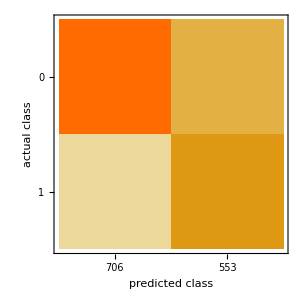

```mathematica
cm["ConfusionMatrixPlot"]
```

#### Мы можем использовать с asm

```mathematica
asm=Select[Import["./programs/dhrystone21.dump","Lines"],StringLength[#]>0&];
```

```mathematica
DeviceRead[device,{
"reset","/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/programs/dhrystone21.hex"
}];
```

```mathematica
labels=Select[Flatten[#,1]&@StringCases[asm,StartOfString~~Shortest[address:HexadecimalCharacter..]~~" <"~~Shortest[label__]~~">"~~Shortest[__]-> {address,label}],FromDigits[#[[1]],16]≠0&];
```

```mathematica
labelsHex=Sort[Map[{FromDigits[#[[1]],16],#[[2]]}&,labels],#1[[1]]<#2[[1]]&];
```

```mathematica
Grid[
BlockMap[#&,Map[#&,DeviceRead[device,{"read_mem",0,32*1024}]],16]
]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 111 | 0 | 0 | 0 | 255 | 255 | 255 | 255
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
111 | 0 | 0 | 11 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0
19 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0
19 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0
19 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0 | 19 | 0 | 0 | 0
151 | 69 | 0 | 0 | 147 | 133 | 5 | 160 | 23 | 102 | 0 | 0 | 19 | 6 | 134 | 39
111 | 0 | 192 | 0 | 35 | 160 | 5 | 0 | 147 | 133 | 69 | 0 | 227 | 156 | 197 | 254
151 | 65 | 0 | 0 | 147 | 129 | 1 | 60 | 23 | 1 | 1 | 0 | 19 | 1 | 129 | 221
183 | 2 | 73 | 0 | 19 | 3 | 16 | 0 | 35 | 160 | 98 | 0 | 183 | 2 | 73 | 0
147 | 130 | 66 | 0 | 19 | 3 | 48 | 6 | 35 | 160 | 98 | 0 | 183 | 2 | 73 | 0
147 | 130 | 2 | 1 | 19 | 3 | 240 | 255 | 35 | 160 | 98 | 0 | 35 | 162 | 98 | 0
19 | 5 | 0 | 0 | 147 | 5 | 0 | 0 | 239 | 0 | 208 | 104 | 111 | 0 | 128 | 17
19 | 1 | 1 | 239 | 35 | 34 | 17 | 0 | 35 | 36 | 33 | 0 | 35 | 38 | 49 | 0
35 | 40 | 65 | 0 | 35 | 42 | 81 | 0 | 35 | 44 | 97 | 0 | 35 | 46 | 113 | 0
35 | 32 | 129 | 2 | 35 | 34 | 145 | 2 | 35 | 36 | 161 | 2 | 35 | 38 | 177 | 2
35 | 40 | 193 | 2 | 35 | 42 | 209 | 2 | 35 | 44 | 225 | 2 | 35 | 46 | 241 | 2
35 | 32 | 1 | 5 | 35 | 34 | 17 | 5 | 35 | 36 | 33 | 5 | 35 | 38 | 49 | 5
35 | 40 | 65 | 5 | 35 | 42 | 81 | 5 | 35 | 44 | 97 | 5 | 35 | 46 | 113 | 5
35 | 32 | 129 | 7 | 35 | 34 | 145 | 7 | 35 | 36 | 161 | 7 | 35 | 38 | 177 | 7
35 | 40 | 193 | 7 | 35 | 42 | 209 | 7 | 35 | 44 | 225 | 7 | 35 | 46 | 241 | 7
115 | 37 | 32 | 52 | 243 | 37 | 16 | 52 | 19 | 6 | 1 | 0 | 239 | 0 | 128 | 8
131 | 32 | 65 | 0 | 3 | 33 | 129 | 0 | 131 | 33 | 193 | 0 | 3 | 34 | 1 | 1
131 | 34 | 65 | 1 | 3 | 35 | 129 | 1 | 131 | 35 | 193 | 1 | 3 | 36 | 1 | 2
131 | 36 | 65 | 2 | 3 | 37 | 129 | 2 | 131 | 37 | 193 | 2 | 3 | 38 | 1 | 3
131 | 38 | 65 | 3 | 3 | 39 | 129 | 3 | 131 | 39 | 193 | 3 | 3 | 40 | 1 | 4
131 | 40 | 65 | 4 | 3 | 41 | 129 | 4 | 131 | 41 | 193 | 4 | 3 | 42 | 1 | 5
131 | 42 | 65 | 5 | 3 | 43 | 129 | 5 | 131 | 43 | 193 | 5 | 3 | 44 | 1 | 6
131 | 44 | 65 | 6 | 3 | 45 | 129 | 6 | 131 | 45 | 193 | 6 | 3 | 46 | 1 | 7
131 | 46 | 65 | 7 | 3 | 47 | 129 | 7 | 131 | 47 | 193 | 7 | 19 | 1 | 1 | 17
115 | 0 | 32 | 48 | 111 | 240 | 31 | 215 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 40 | 2 | 4 | 147 | 2 | 2 | 0 | 19 | 7 | 24 | 0 | 51 | 131 | 2 | 1
35 | 32 | 226 | 4 | 35 | 0 | 163 | 0 | 147 | 3 | 160 | 0 | 99 | 8 | 117 | 0
19 | 5 | 0 | 4 | 99 | 6 | 167 | 0 | 103 | 128 | 0 | 0 | 99 | 84 | 224 | 16
19 | 126 | 119 | 0 | 147 | 7 | 2 | 0 | 183 | 14 | 0 | 240 | 19 | 15 | 247 | 255
99 | 4 | 14 | 10 | 147 | 15 | 16 | 0 | 99 | 6 | 254 | 9 | 147 | 5 | 32 | 0
99 | 10 | 190 | 6 | 19 | 8 | 48 | 0 | 99 | 14 | 14 | 5 | 147 | 6 | 64 | 0
99 | 2 | 222 | 4 | 147 | 2 | 80 | 0 | 99 | 6 | 94 | 2 | 19 | 3 | 96 | 0
99 | 10 | 110 | 0 | 131 | 195 | 7 | 0 | 19 | 7 | 15 | 0 | 147 | 135 | 23 | 0
35 | 128 | 126 | 0 | 3 | 197 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 174 | 0 | 131 | 200 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 30 | 1 | 3 | 206 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 206 | 1 | 3 | 207 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 238 | 1 | 131 | 207 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 254 | 1 | 147 | 135 | 23 | 0 | 131 | 197 | 247 | 255 | 19 | 7 | 247 | 255
35 | 128 | 190 | 0 | 99 | 8 | 7 | 4 | 3 | 200 | 7 | 0 | 147 | 135 | 135 | 0
19 | 7 | 135 | 255 | 35 | 128 | 14 | 1 | 131 | 198 | 151 | 255 | 35 | 128 | 222 | 0
131 | 194 | 167 | 255 | 35 | 128 | 94 | 0 | 3 | 195 | 183 | 255 | 35 | 128 | 110 | 0
131 | 195 | 199 | 255 | 35 | 128 | 126 | 0 | 3 | 197 | 215 | 255 | 35 | 128 | 174 | 0
131 | 200 | 231 | 255 | 35 | 128 | 30 | 1 | 3 | 206 | 247 | 255 | 35 | 128 | 206 | 1
227 | 28 | 7 | 250 | 35 | 32 | 2 | 4 | 103 | 128 | 0 | 0 | 147 | 7 | 48 | 4
99 | 6 | 245 | 0 | 19 | 5 | 0 | 0 | 103 | 128 | 0 | 0 | 183 | 66 | 0 | 0
35 | 134 | 162 | 194 | 19 | 5 | 16 | 0 | 103 | 128 | 0 | 0 | 19 | 1 | 1 | 235
35 | 32 | 33 | 21 | 35 | 46 | 177 | 17 | 147 | 13 | 2 | 0 | 35 | 38 | 17 | 20
35 | 36 | 129 | 20 | 147 | 7 | 16 | 6 | 147 | 128 | 13 | 4 | 35 | 34 | 145 | 19
35 | 34 | 145 | 20 | 35 | 46 | 49 | 19 | 35 | 44 | 65 | 19 | 35 | 42 | 81 | 19
35 | 40 | 97 | 19 | 35 | 38 | 113 | 19 | 35 | 36 | 129 | 19 | 35 | 32 | 161 | 19
147 | 12 | 5 | 0 | 35 | 36 | 177 | 0 | 35 | 38 | 241 | 0 | 35 | 34 | 17 | 0
131 | 194 | 12 | 0 | 19 | 7 | 80 | 2 | 99 | 138 | 226 | 18 | 99 | 132 | 2 | 24
3 | 44 | 2 | 4 | 147 | 11 | 160 | 0 | 147 | 140 | 28 | 0 | 19 | 7 | 28 | 0
51 | 133 | 141 | 1 | 35 | 32 | 226 | 4 | 35 | 0 | 85 | 0 | 99 | 142 | 114 | 21
19 | 8 | 0 | 4 | 227 | 22 | 7 | 253 | 19 | 125 | 119 | 0 | 147 | 7 | 2 | 0
55 | 15 | 0 | 240 | 147 | 0 | 247 | 255 | 99 | 12 | 13 | 8 | 19 | 6 | 16 | 0
99 | 14 | 205 | 6 | 147 | 2 | 32 | 0 | 99 | 2 | 93 | 6 | 147 | 6 | 48 | 0
99 | 6 | 221 | 4 | 19 | 3 | 64 | 0 | 99 | 10 | 109 | 2 | 147 | 4 | 80 | 0
99 | 14 | 157 | 0 | 147 | 3 | 96 | 0 | 99 | 28 | 125 | 20 | 131 | 206 | 7 | 0
19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 0 | 223 | 1 | 3 | 202 | 7 | 0
19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 0 | 79 | 1 | 131 | 201 | 7 | 0
19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 0 | 63 | 1 | 131 | 202 | 7 | 0
19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 0 | 95 | 1 | 131 | 197 | 7 | 0
19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 0 | 191 | 0 | 147 | 135 | 23 | 0
131 | 200 | 247 | 255 | 19 | 7 | 247 | 255 | 35 | 0 | 31 | 1 | 99 | 8 | 7 | 4
3 | 203 | 7 | 0 | 147 | 135 | 135 | 0 | 19 | 7 | 135 | 255 | 35 | 0 | 111 | 1
131 | 207 | 151 | 255 | 35 | 0 | 255 | 1 | 3 | 204 | 167 | 255 | 35 | 0 | 143 | 1
131 | 203 | 183 | 255 | 35 | 0 | 127 | 1 | 3 | 197 | 199 | 255 | 35 | 0 | 175 | 0
3 | 200 | 215 | 255 | 35 | 0 | 15 | 1 | 3 | 205 | 231 | 255 | 35 | 0 | 175 | 1
131 | 192 | 247 | 255 | 35 | 0 | 31 | 0 | 227 | 28 | 7 | 250 | 35 | 32 | 2 | 4
131 | 194 | 12 | 0 | 19 | 7 | 80 | 2 | 227 | 154 | 226 | 236 | 19 | 139 | 28 | 0
183 | 54 | 0 | 0 | 147 | 15 | 11 | 0 | 147 | 11 | 0 | 2 | 147 | 4 | 240 | 255
19 | 12 | 240 | 255 | 19 | 5 | 0 | 0 | 147 | 7 | 80 | 5 | 147 | 133 | 6 | 204
147 | 8 | 144 | 0 | 3 | 198 | 15 | 0 | 147 | 140 | 31 | 0 | 19 | 3 | 214 | 253
147 | 115 | 243 | 15 | 99 | 234 | 119 | 88 | 19 | 152 | 35 | 0 | 179 | 9 | 184 | 0
3 | 170 | 9 | 0 | 103 | 0 | 10 | 0 | 227 | 72 | 224 | 234 | 35 | 32 | 2 | 4
111 | 240 | 31 | 250 | 131 | 32 | 193 | 20 | 3 | 36 | 129 | 20 | 131 | 36 | 65 | 20
3 | 41 | 1 | 20 | 131 | 41 | 193 | 19 | 3 | 42 | 129 | 19 | 131 | 42 | 65 | 19
3 | 43 | 1 | 19 | 131 | 43 | 193 | 18 | 3 | 44 | 129 | 18 | 131 | 44 | 65 | 18
3 | 45 | 1 | 18 | 131 | 45 | 193 | 17 | 19 | 1 | 1 | 21 | 103 | 128 | 0 | 0
3 | 206 | 7 | 0 | 19 | 135 | 0 | 0 | 147 | 135 | 23 | 0 | 35 | 0 | 207 | 1
111 | 240 | 223 | 233 | 99 | 84 | 12 | 0 | 19 | 12 | 0 | 0 | 147 | 143 | 12 | 0
111 | 240 | 95 | 247 | 147 | 4 | 16 | 6 | 35 | 38 | 145 | 0 | 19 | 13 | 0 | 1
147 | 0 | 16 | 0 | 99 | 214 | 160 | 116 | 3 | 43 | 129 | 0 | 19 | 14 | 123 | 0
147 | 126 | 142 | 255 | 131 | 169 | 14 | 0 | 3 | 171 | 78 | 0 | 19 | 133 | 142 | 0
35 | 36 | 161 | 0 | 19 | 90 | 253 | 65 | 19 | 6 | 13 | 0 | 147 | 6 | 10 | 0
19 | 133 | 9 | 0 | 147 | 5 | 11 | 0 | 239 | 32 | 0 | 16 | 35 | 40 | 161 | 0
99 | 100 | 75 | 113 | 99 | 0 | 106 | 113 | 147 | 10 | 65 | 1 | 147 | 4 | 16 | 0
19 | 6 | 13 | 0 | 147 | 6 | 10 | 0 | 19 | 133 | 9 | 0 | 147 | 5 | 11 | 0
239 | 16 | 16 | 74 | 19 | 6 | 13 | 0 | 147 | 6 | 10 | 0 | 147 | 9 | 5 | 0
19 | 139 | 5 | 0 | 239 | 32 | 64 | 12 | 35 | 160 | 170 | 0 | 147 | 132 | 20 | 0
147 | 138 | 74 | 0 | 99 | 102 | 75 | 1 | 227 | 20 | 106 | 253 | 227 | 242 | 169 | 253
19 | 3 | 0 | 4 | 183 | 3 | 0 | 240 | 99 | 210 | 132 | 3 | 131 | 37 | 2 | 4
19 | 136 | 21 | 0 | 179 | 136 | 189 | 0 | 35 | 32 | 2 | 5 | 35 | 128 | 120 | 1
99 | 10 | 104 | 6 | 19 | 12 | 252 | 255 | 227 | 194 | 132 | 255 | 131 | 38 | 193 | 0
147 | 155 | 36 | 0 | 19 | 12 | 1 | 17 | 51 | 13 | 124 | 1 | 147 | 7 | 205 | 239
147 | 3 | 193 | 0 | 147 | 8 | 144 | 0 | 147 | 143 | 102 | 255 | 19 | 8 | 160 | 0
183 | 5 | 0 | 240 | 19 | 3 | 0 | 4 | 227 | 140 | 243 | 208 | 3 | 167 | 7 | 0
19 | 15 | 0 | 3 | 99 | 244 | 232 | 0 | 19 | 143 | 15 | 0 | 3 | 38 | 2 | 4
179 | 0 | 231 | 1 | 147 | 6 | 22 | 0 | 179 | 130 | 205 | 0 | 35 | 32 | 210 | 4
35 | 128 | 18 | 0 | 99 | 132 | 0 | 65 | 99 | 132 | 102 | 64 | 147 | 135 | 199 | 255
111 | 240 | 159 | 252 | 131 | 47 | 65 | 0 | 147 | 135 | 13 | 0 | 51 | 141 | 191 | 65
19 | 127 | 125 | 0 | 99 | 8 | 15 | 8 | 19 | 6 | 16 | 0 | 99 | 10 | 207 | 6
147 | 0 | 32 | 0 | 99 | 0 | 31 | 6 | 19 | 7 | 48 | 0 | 99 | 6 | 239 | 4
147 | 2 | 64 | 0 | 99 | 12 | 95 | 2 | 147 | 6 | 80 | 0 | 99 | 2 | 223 | 2
19 | 14 | 96 | 0 | 99 | 8 | 207 | 1 | 131 | 206 | 13 | 0 | 147 | 135 | 29 | 0
35 | 128 | 211 | 1 | 3 | 197 | 7 | 0 | 147 | 135 | 23 | 0 | 35 | 128 | 163 | 0
3 | 202 | 7 | 0 | 147 | 135 | 23 | 0 | 35 | 128 | 67 | 1 | 131 | 201 | 7 | 0
147 | 135 | 23 | 0 | 35 | 128 | 51 | 1 | 3 | 203 | 7 | 0 | 147 | 135 | 23 | 0
35 | 128 | 99 | 1 | 131 | 202 | 7 | 0 | 147 | 135 | 23 | 0 | 35 | 128 | 83 | 1
147 | 135 | 23 | 0 | 131 | 197 | 247 | 255 | 35 | 128 | 179 | 0 | 3 | 40 | 65 | 0
99 | 136 | 7 | 5 | 131 | 200 | 7 | 0 | 147 | 135 | 135 | 0 | 35 | 128 | 19 | 1
131 | 207 | 151 | 255 | 35 | 128 | 243 | 1 | 3 | 205 | 167 | 255 | 35 | 128 | 163 | 1
3 | 207 | 183 | 255 | 35 | 128 | 227 | 1 | 3 | 198 | 199 | 255 | 35 | 128 | 195 | 0
131 | 192 | 215 | 255 | 35 | 128 | 19 | 0 | 3 | 199 | 231 | 255 | 35 | 128 | 227 | 0
131 | 194 | 247 | 255 | 35 | 128 | 83 | 0 | 131 | 38 | 65 | 0 | 227 | 156 | 215 | 250
35 | 32 | 2 | 4 | 19 | 12 | 252 | 255 | 111 | 240 | 31 | 234 | 147 | 143 | 12 | 0
147 | 11 | 0 | 3 | 111 | 240 | 31 | 212 | 131 | 41 | 129 | 0 | 147 | 143 | 12 | 0
131 | 164 | 9 | 0 | 147 | 138 | 73 | 0 | 35 | 36 | 81 | 1 | 227 | 84 | 12 | 210
19 | 140 | 4 | 0 | 147 | 4 | 240 | 255 | 111 | 240 | 223 | 209 | 131 | 206 | 31 | 0
147 | 4 | 6 | 253 | 147 | 143 | 12 | 0 | 19 | 131 | 14 | 253 | 227 | 224 | 104 | 254
147 | 156 | 36 | 0 | 179 | 132 | 156 | 0 | 147 | 147 | 20 | 0 | 147 | 143 | 31 | 0
51 | 142 | 211 | 1 | 131 | 206 | 15 | 0 | 147 | 4 | 14 | 253 | 19 | 138 | 14 | 253
227 | 240 | 72 | 255 | 111 | 240 | 159 | 251 | 147 | 5 | 0 | 0 | 19 | 5 | 80 | 2
239 | 240 | 31 | 156 | 111 | 240 | 223 | 182 | 3 | 37 | 129 | 0 | 3 | 43 | 5 | 0
19 | 10 | 69 | 0 | 99 | 12 | 11 | 78 | 99 | 82 | 128 | 77 | 147 | 5 | 208 | 2
99 | 158 | 187 | 80 | 3 | 78 | 11 | 0 | 147 | 14 | 14 | 0 | 99 | 6 | 14 | 4
19 | 15 | 240 | 255 | 147 | 15 | 160 | 0 | 183 | 0 | 0 | 240 | 147 | 2 | 0 | 4
99 | 212 | 4 | 70 | 131 | 39 | 2 | 4 | 19 | 135 | 23 | 0 | 179 | 134 | 253 | 0
35 | 32 | 226 | 4 | 35 | 128 | 198 | 1 | 99 | 130 | 254 | 53 | 99 | 2 | 87 | 52
19 | 11 | 27 | 0 | 3 | 78 | 11 | 0 | 19 | 12 | 252 | 255 | 147 | 14 | 14 | 0
227 | 24 | 14 | 252 | 99 | 94 | 128 | 17 | 19 | 123 | 124 | 0 | 147 | 4 | 252 | 255
99 | 4 | 11 | 10 | 19 | 15 | 16 | 0 | 99 | 6 | 235 | 9 | 147 | 15 | 32 | 0
99 | 10 | 251 | 7 | 147 | 0 | 48 | 0 | 99 | 14 | 27 | 4 | 147 | 2 | 64 | 0
99 | 2 | 91 | 4 | 147 | 10 | 80 | 0 | 99 | 6 | 91 | 3 | 147 | 11 | 96 | 0
99 | 10 | 123 | 1 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 144
19 | 140 | 4 | 0 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 143
19 | 12 | 252 | 255 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 142
19 | 12 | 252 | 255 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 141
19 | 12 | 252 | 255 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 140
19 | 12 | 252 | 255 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 139
19 | 12 | 252 | 255 | 19 | 12 | 252 | 255 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2
239 | 240 | 31 | 138 | 99 | 6 | 12 | 6 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2
239 | 240 | 31 | 137 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 136
147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 159 | 135 | 147 | 5 | 0 | 0
19 | 5 | 0 | 2 | 239 | 240 | 223 | 134 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2
239 | 240 | 31 | 134 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 95 | 133
147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 159 | 132 | 19 | 12 | 140 | 255
147 | 5 | 0 | 0 | 19 | 5 | 0 | 2 | 239 | 240 | 159 | 131 | 227 | 30 | 12 | 248
35 | 36 | 65 | 1 | 111 | 240 | 223 | 157 | 19 | 13 | 160 | 0 | 111 | 240 | 95 | 189
147 | 143 | 12 | 0 | 147 | 11 | 208 | 2 | 111 | 240 | 223 | 178 | 147 | 15 | 16 | 4
35 | 38 | 241 | 1 | 19 | 13 | 0 | 1 | 111 | 240 | 159 | 187 | 3 | 47 | 129 | 0
147 | 5 | 0 | 0 | 3 | 37 | 15 | 0 | 147 | 10 | 79 | 0 | 239 | 240 | 79 | 255
35 | 36 | 81 | 1 | 111 | 240 | 223 | 153 | 147 | 6 | 16 | 0 | 99 | 218 | 166 | 48
3 | 39 | 129 | 0 | 19 | 3 | 119 | 0 | 147 | 115 | 131 | 255 | 131 | 169 | 3 | 0
3 | 171 | 67 | 0 | 19 | 136 | 131 | 0 | 35 | 36 | 1 | 1 | 99 | 80 | 11 | 2
147 | 5 | 0 | 0 | 19 | 5 | 208 | 2 | 239 | 240 | 143 | 251 | 179 | 9 | 48 | 65
179 | 53 | 48 | 1 | 179 | 8 | 96 | 65 | 51 | 139 | 184 | 64 | 19 | 13 | 160 | 0
111 | 240 | 95 | 183 | 19 | 5 | 21 | 0 | 147 | 143 | 12 | 0 | 111 | 240 | 159 | 170
19 | 13 | 128 | 0 | 111 | 240 | 223 | 179 | 147 | 5 | 0 | 0 | 19 | 5 | 0 | 3
239 | 240 | 15 | 248 | 147 | 5 | 0 | 0 | 19 | 5 | 128 | 7 | 239 | 240 | 79 | 247
131 | 46 | 129 | 0 | 19 | 14 | 16 | 6 | 19 | 13 | 0 | 1 | 35 | 38 | 193 | 1
147 | 132 | 78 | 0 | 3 | 42 | 129 | 0 | 19 | 11 | 0 | 0 | 35 | 36 | 145 | 0
131 | 41 | 10 | 0 | 111 | 240 | 31 | 178 | 147 | 5 | 0 | 0 | 19 | 5 | 80 | 2
239 | 240 | 15 | 244 | 147 | 12 | 11 | 0 | 111 | 240 | 159 | 142 | 99 | 82 | 208 | 16
147 | 244 | 118 | 0 | 19 | 7 | 2 | 0 | 19 | 142 | 246 | 255 | 99 | 132 | 4 | 10
147 | 14 | 16 | 0 | 99 | 134 | 212 | 9 | 19 | 5 | 32 | 0 | 99 | 138 | 164 | 6
19 | 10 | 48 | 0 | 99 | 142 | 68 | 5 | 147 | 9 | 64 | 0 | 99 | 130 | 52 | 5
19 | 11 | 80 | 0 | 99 | 134 | 100 | 3 | 147 | 10 | 96 | 0 | 99 | 138 | 84 | 1
131 | 75 | 7 | 0 | 147 | 6 | 14 | 0 | 19 | 7 | 23 | 0 | 35 | 128 | 117 | 1
3 | 76 | 7 | 0 | 147 | 134 | 246 | 255 | 19 | 7 | 23 | 0 | 35 | 128 | 133 | 1
3 | 77 | 7 | 0 | 147 | 134 | 246 | 255 | 19 | 7 | 23 | 0 | 35 | 128 | 165 | 1
3 | 79 | 7 | 0 | 147 | 134 | 246 | 255 | 19 | 7 | 23 | 0 | 35 | 128 | 229 | 1
3 | 70 | 7 | 0 | 147 | 134 | 246 | 255 | 19 | 7 | 23 | 0 | 35 | 128 | 197 | 0
131 | 64 | 7 | 0 | 147 | 134 | 246 | 255 | 19 | 7 | 23 | 0 | 35 | 128 | 21 | 0
19 | 7 | 23 | 0 | 131 | 66 | 247 | 255 | 147 | 134 | 246 | 255 | 35 | 128 | 85 | 0
99 | 136 | 6 | 4 | 131 | 68 | 7 | 0 | 19 | 7 | 135 | 0 | 147 | 134 | 134 | 255
35 | 128 | 149 | 0 | 3 | 78 | 151 | 255 | 35 | 128 | 197 | 1 | 131 | 78 | 167 | 255
35 | 128 | 213 | 1 | 3 | 69 | 183 | 255 | 35 | 128 | 165 | 0 | 3 | 74 | 199 | 255
35 | 128 | 69 | 1 | 131 | 73 | 215 | 255 | 35 | 128 | 53 | 1 | 3 | 75 | 231 | 255
35 | 128 | 101 | 1 | 131 | 74 | 247 | 255 | 35 | 128 | 85 | 1 | 227 | 156 | 6 | 250
35 | 32 | 2 | 4 | 147 | 135 | 199 | 255 | 111 | 240 | 31 | 172 | 99 | 82 | 224 | 16
19 | 118 | 119 | 0 | 147 | 7 | 2 | 0 | 19 | 3 | 247 | 255 | 99 | 4 | 6 | 10
147 | 3 | 16 | 0 | 99 | 6 | 118 | 8 | 19 | 8 | 32 | 0 | 99 | 10 | 6 | 7
147 | 9 | 48 | 0 | 99 | 14 | 54 | 5 | 19 | 13 | 64 | 0 | 99 | 2 | 166 | 5
19 | 5 | 80 | 0 | 99 | 6 | 166 | 2 | 147 | 5 | 96 | 0 | 99 | 10 | 182 | 0
131 | 200 | 7 | 0 | 19 | 7 | 3 | 0 | 147 | 135 | 23 | 0 | 35 | 128 | 16 | 1
131 | 202 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 128 | 80 | 1
131 | 203 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 128 | 112 | 1
3 | 206 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 128 | 192 | 1
131 | 206 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 128 | 208 | 1
131 | 198 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0 | 35 | 128 | 208 | 0
147 | 135 | 23 | 0 | 3 | 198 | 247 | 255 | 19 | 7 | 247 | 255 | 35 | 128 | 192 | 0
99 | 8 | 7 | 4 | 3 | 195 | 7 | 0 | 147 | 135 | 135 | 0 | 19 | 7 | 135 | 255
35 | 128 | 96 | 0 | 131 | 195 | 151 | 255 | 35 | 128 | 112 | 0 | 3 | 200 | 167 | 255
35 | 128 | 0 | 1 | 131 | 201 | 183 | 255 | 35 | 128 | 48 | 1 | 3 | 205 | 199 | 255
35 | 128 | 160 | 1 | 3 | 197 | 215 | 255 | 35 | 128 | 160 | 0 | 131 | 197 | 231 | 255
35 | 128 | 176 | 0 | 131 | 200 | 247 | 255 | 35 | 128 | 16 | 1 | 227 | 28 | 7 | 250
35 | 32 | 2 | 4 | 111 | 240 | 223 | 187 | 147 | 132 | 244 | 255 | 227 | 156 | 228 | 185
111 | 240 | 95 | 188 | 227 | 242 | 169 | 145 | 147 | 4 | 16 | 0 | 111 | 240 | 95 | 148
131 | 34 | 129 | 0 | 147 | 132 | 66 | 0 | 111 | 240 | 223 | 217 | 147 | 139 | 9 | 0
99 | 212 | 9 | 0 | 147 | 11 | 0 | 0 | 51 | 140 | 121 | 65 | 3 | 78 | 11 | 0
147 | 14 | 14 | 0 | 227 | 22 | 14 | 180 | 35 | 36 | 65 | 1 | 111 | 240 | 79 | 232
3 | 38 | 129 | 0 | 147 | 7 | 70 | 0 | 99 | 10 | 5 | 2 | 131 | 41 | 6 | 0
35 | 36 | 241 | 0 | 19 | 219 | 249 | 65 | 111 | 240 | 95 | 207 | 99 | 86 | 128 | 1
147 | 8 | 208 | 2 | 99 | 144 | 27 | 3 | 55 | 59 | 0 | 0 | 19 | 11 | 203 | 1
19 | 14 | 128 | 2 | 147 | 14 | 128 | 2 | 111 | 240 | 159 | 176 | 3 | 38 | 129 | 0
111 | 240 | 223 | 252 | 183 | 58 | 0 | 0 | 19 | 139 | 202 | 1 | 147 | 133 | 4 | 0
19 | 5 | 11 | 0 | 239 | 0 | 144 | 54 | 179 | 9 | 172 | 64 | 19 | 141 | 9 | 0
227 | 94 | 160 | 247 | 147 | 5 | 0 | 0 | 19 | 133 | 11 | 0 | 239 | 240 | 79 | 198
19 | 13 | 253 | 255 | 111 | 240 | 223 | 254 | 19 | 1 | 1 | 252 | 19 | 3 | 65 | 2
35 | 34 | 177 | 2 | 147 | 5 | 3 | 0 | 35 | 46 | 17 | 0 | 35 | 36 | 193 | 2
35 | 38 | 209 | 2 | 35 | 40 | 225 | 2 | 35 | 42 | 241 | 2 | 35 | 44 | 1 | 3
35 | 46 | 17 | 3 | 35 | 38 | 97 | 0 | 239 | 240 | 79 | 216 | 131 | 32 | 193 | 1
19 | 5 | 0 | 0 | 19 | 1 | 1 | 4 | 103 | 128 | 0 | 0 | 3 | 40 | 2 | 4
147 | 2 | 2 | 0 | 19 | 7 | 24 | 0 | 51 | 131 | 2 | 1 | 35 | 32 | 226 | 4
35 | 0 | 163 | 0 | 147 | 3 | 160 | 0 | 99 | 10 | 117 | 0 | 19 | 5 | 0 | 4
99 | 8 | 167 | 0 | 19 | 5 | 0 | 0 | 103 | 128 | 0 | 0 | 99 | 84 | 224 | 16
19 | 126 | 119 | 0 | 147 | 7 | 2 | 0 | 183 | 14 | 0 | 240 | 19 | 15 | 247 | 255
99 | 4 | 14 | 10 | 147 | 15 | 16 | 0 | 99 | 6 | 254 | 9 | 147 | 5 | 32 | 0
99 | 10 | 190 | 6 | 19 | 8 | 48 | 0 | 99 | 14 | 14 | 5 | 147 | 6 | 64 | 0
99 | 2 | 222 | 4 | 147 | 2 | 80 | 0 | 99 | 6 | 94 | 2 | 19 | 3 | 96 | 0
99 | 10 | 110 | 0 | 131 | 195 | 7 | 0 | 19 | 7 | 15 | 0 | 147 | 135 | 23 | 0
35 | 128 | 126 | 0 | 3 | 197 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 174 | 0 | 131 | 200 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 30 | 1 | 3 | 206 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 206 | 1 | 3 | 207 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 238 | 1 | 131 | 207 | 7 | 0 | 19 | 7 | 247 | 255 | 147 | 135 | 23 | 0
35 | 128 | 254 | 1 | 147 | 135 | 23 | 0 | 131 | 197 | 247 | 255 | 19 | 7 | 247 | 255
35 | 128 | 190 | 0 | 99 | 8 | 7 | 4 | 3 | 200 | 7 | 0 | 147 | 135 | 135 | 0
19 | 7 | 135 | 255 | 35 | 128 | 14 | 1 | 131 | 198 | 151 | 255 | 35 | 128 | 222 | 0
131 | 194 | 167 | 255 | 35 | 128 | 94 | 0 | 3 | 195 | 183 | 255 | 35 | 128 | 110 | 0
131 | 195 | 199 | 255 | 35 | 128 | 126 | 0 | 3 | 197 | 215 | 255 | 35 | 128 | 174 | 0
131 | 200 | 231 | 255 | 35 | 128 | 30 | 1 | 3 | 206 | 247 | 255 | 35 | 128 | 206 | 1
227 | 28 | 7 | 250 | 35 | 32 | 2 | 4 | 19 | 5 | 0 | 0 | 103 | 128 | 0 | 0
0 | 0 | 0 | 0 | 55 | 51 | 0 | 0 | 19 | 1 | 1 | 244 | 147 | 6 | 67 | 2
35 | 46 | 17 | 10 | 35 | 38 | 49 | 11 | 35 | 36 | 65 | 11 | 131 | 169 | 70 | 0
3 | 42 | 67 | 2 | 183 | 64 | 0 | 0 | 35 | 44 | 129 | 10 | 35 | 40 | 33 | 11
35 | 44 | 129 | 9 | 3 | 164 | 198 | 0 | 19 | 140 | 64 | 195 | 3 | 169 | 134 | 0
35 | 42 | 145 | 10 | 35 | 34 | 81 | 11 | 35 | 32 | 97 | 11 | 35 | 46 | 113 | 9
35 | 42 | 145 | 9 | 35 | 40 | 161 | 9 | 35 | 38 | 177 | 9 | 55 | 56 | 0 | 0
183 | 68 | 0 | 0 | 147 | 10 | 12 | 3 | 55 | 75 | 0 | 0 | 147 | 11 | 32 | 0
147 | 12 | 128 | 2 | 19 | 7 | 8 | 90 | 131 | 162 | 70 | 1 | 35 | 32 | 76 | 5
35 | 34 | 60 | 5 | 35 | 36 | 139 | 195 | 35 | 162 | 84 | 195 | 35 | 40 | 140 | 3
35 | 42 | 12 | 2 | 35 | 44 | 124 | 3 | 35 | 46 | 156 | 3 | 131 | 163 | 6 | 1
131 | 175 | 134 | 1 | 3 | 223 | 198 | 1 | 131 | 206 | 230 | 1 | 3 | 46 | 8 | 90
131 | 40 | 71 | 0 | 35 | 36 | 44 | 5 | 3 | 40 | 135 | 0 | 3 | 42 | 199 | 0
131 | 41 | 7 | 1 | 3 | 41 | 71 | 1 | 3 | 83 | 199 | 1 | 35 | 38 | 140 | 4
3 | 36 | 135 | 1 | 3 | 71 | 231 | 1 | 55 | 77 | 0 | 0 | 35 | 42 | 92 | 4
19 | 13 | 205 | 213 | 147 | 6 | 160 | 0 | 147 | 2 | 64 | 31 | 35 | 40 | 124 | 4
35 | 44 | 252 | 5 | 35 | 30 | 236 | 5 | 35 | 15 | 220 | 5 | 35 | 32 | 193 | 7
35 | 34 | 17 | 7 | 35 | 36 | 1 | 7 | 35 | 38 | 65 | 7 | 35 | 40 | 49 | 7
35 | 42 | 33 | 7 | 35 | 44 | 129 | 6 | 35 | 30 | 97 | 6 | 35 | 15 | 225 | 6
35 | 46 | 221 | 100 | 147 | 3 | 16 | 0 | 35 | 40 | 81 | 0 | 99 | 208 | 163 | 2
3 | 165 | 69 | 0 | 35 | 42 | 241 | 0 | 35 | 38 | 193 | 0 | 239 | 0 | 144 | 6
131 | 39 | 65 | 1 | 3 | 38 | 193 | 0 | 35 | 40 | 161 | 0 | 183 | 58 | 0 | 0
19 | 133 | 74 | 34 | 35 | 42 | 241 | 0 | 35 | 38 | 193 | 0 | 239 | 240 | 223 | 209
55 | 53 | 0 | 0 | 19 | 5 | 69 | 4 | 239 | 240 | 31 | 209 | 19 | 133 | 74 | 34
239 | 240 | 159 | 208 | 183 | 53 | 0 | 0 | 19 | 133 | 69 | 7 | 239 | 240 | 223 | 207
19 | 133 | 74 | 34 | 239 | 240 | 95 | 207 | 3 | 43 | 1 | 1 | 55 | 54 | 0 | 0
19 | 5 | 70 | 10 | 147 | 5 | 11 | 0 | 239 | 240 | 31 | 206 | 243 | 47 | 0 | 192
183 | 78 | 0 | 0 | 183 | 71 | 0 | 0 | 19 | 15 | 16 | 0 | 35 | 174 | 238 | 193
35 | 160 | 247 | 195 | 3 | 40 | 193 | 0 | 131 | 46 | 65 | 1 | 99 | 14 | 11 | 58
183 | 61 | 0 | 0 | 147 | 140 | 13 | 92 | 183 | 48 | 0 | 0 | 131 | 168 | 0 | 94
131 | 171 | 13 | 92 | 3 | 170 | 140 | 0 | 131 | 169 | 204 | 0 | 3 | 169 | 12 | 1
3 | 168 | 76 | 0 | 3 | 164 | 76 | 1 | 3 | 163 | 140 | 1 | 3 | 215 | 204 | 1
183 | 70 | 0 | 0 | 183 | 83 | 0 | 0 | 35 | 44 | 113 | 1 | 35 | 32 | 65 | 3
35 | 34 | 49 | 3 | 35 | 36 | 33 | 3 | 35 | 44 | 17 | 3 | 35 | 46 | 1 | 1
35 | 38 | 129 | 2 | 35 | 40 | 97 | 2 | 35 | 27 | 225 | 2 | 183 | 75 | 0 | 0
35 | 42 | 209 | 0 | 19 | 10 | 1 | 4 | 147 | 10 | 1 | 6 | 55 | 75 | 0 | 0
147 | 137 | 195 | 213 | 55 | 73 | 0 | 0 | 35 | 46 | 17 | 3 | 111 | 0 | 64 | 14
131 | 160 | 3 | 0 | 183 | 77 | 0 | 0 | 3 | 164 | 205 | 193 | 131 | 175 | 0 | 0
3 | 165 | 192 | 1 | 3 | 175 | 64 | 0 | 131 | 174 | 128 | 0 | 3 | 174 | 192 | 0
3 | 163 | 0 | 1 | 131 | 168 | 64 | 1 | 3 | 168 | 128 | 1 | 131 | 165 | 0 | 2
3 | 166 | 64 | 2 | 131 | 162 | 128 | 2 | 3 | 167 | 192 | 2 | 35 | 160 | 243 | 1
35 | 174 | 163 | 0 | 35 | 162 | 227 | 1 | 35 | 164 | 211 | 1 | 35 | 166 | 195 | 1
35 | 168 | 99 | 0 | 35 | 170 | 19 | 1 | 35 | 172 | 3 | 1 | 35 | 160 | 179 | 2
35 | 162 | 195 | 2 | 35 | 164 | 83 | 2 | 35 | 166 | 227 | 2 | 19 | 5 | 16 | 4
239 | 240 | 207 | 149 | 147 | 13 | 16 | 0 | 147 | 15 | 48 | 0 | 99 | 4 | 181 | 31
19 | 5 | 32 | 4 | 35 | 38 | 241 | 1 | 239 | 240 | 79 | 148 | 3 | 38 | 193 | 0
99 | 2 | 181 | 37 | 147 | 18 | 22 | 0 | 51 | 135 | 194 | 0 | 147 | 6 | 112 | 0
51 | 72 | 215 | 2 | 147 | 7 | 151 | 255 | 131 | 207 | 203 | 194 | 147 | 144 | 55 | 0
51 | 143 | 240 | 64 | 147 | 3 | 16 | 4 | 179 | 14 | 15 | 65 | 99 | 152 | 127 | 0
3 | 46 | 9 | 193 | 147 | 8 | 152 | 0 | 51 | 136 | 200 | 65 | 131 | 37 | 1 | 1
19 | 4 | 20 | 0 | 55 | 69 | 0 | 0 | 35 | 46 | 133 | 192 | 99 | 236 | 133 | 38
131 | 194 | 236 | 1 | 3 | 38 | 65 | 1 | 131 | 39 | 129 | 1 | 3 | 47 | 193 | 1
131 | 46 | 1 | 2 | 3 | 46 | 65 | 2 | 131 | 45 | 129 | 2 | 131 | 32 | 193 | 2
131 | 40 | 1 | 3 | 3 | 88 | 97 | 3 | 3 | 69 | 33 | 6 | 147 | 5 | 16 | 4
147 | 15 | 32 | 4 | 35 | 134 | 187 | 194 | 35 | 10 | 246 | 193 | 35 | 32 | 241 | 4
35 | 34 | 225 | 5 | 35 | 36 | 209 | 5 | 35 | 38 | 193 | 5 | 35 | 40 | 177 | 5
35 | 42 | 17 | 4 | 35 | 44 | 17 | 5 | 35 | 30 | 1 | 5 | 35 | 15 | 81 | 4
19 | 4 | 144 | 5 | 99 | 8 | 133 | 30 | 147 | 5 | 10 | 0 | 19 | 133 | 10 | 0
239 | 0 | 144 | 28 | 3 | 35 | 205 | 101 | 131 | 163 | 68 | 194 | 19 | 7 | 112 | 0
147 | 2 | 128 | 0 | 147 | 6 | 19 | 0 | 35 | 44 | 92 | 14 | 35 | 32 | 93 | 102
35 | 34 | 93 | 102 | 35 | 46 | 221 | 100 | 35 | 160 | 233 | 96 | 35 | 34 | 236 | 8
35 | 32 | 236 | 8 | 131 | 173 | 3 | 0 | 131 | 167 | 67 | 0 | 131 | 175 | 131 | 0
3 | 175 | 3 | 1 | 131 | 174 | 67 | 1 | 3 | 174 | 131 | 1 | 3 | 164 | 195 | 1
131 | 168 | 3 | 2 | 3 | 168 | 67 | 2 | 3 | 166 | 131 | 2 | 19 | 3 | 80 | 0
19 | 37 | 21 | 0 | 131 | 165 | 195 | 2 | 35 | 44 | 171 | 192 | 35 | 162 | 253 | 0
35 | 40 | 105 | 192 | 35 | 160 | 189 | 1 | 35 | 164 | 253 | 1 | 35 | 168 | 237 | 1
35 | 170 | 221 | 1 | 35 | 172 | 205 | 1 | 35 | 174 | 141 | 0 | 35 | 160 | 29 | 3
35 | 162 | 13 | 3 | 35 | 164 | 205 | 2 | 3 | 167 | 3 | 0 | 147 | 6 | 16 | 1
35 | 166 | 189 | 2 | 35 | 160 | 237 | 0 | 131 | 162 | 3 | 0 | 35 | 166 | 109 | 0
35 | 160 | 93 | 0 | 35 | 166 | 211 | 0 | 131 | 167 | 77 | 0 | 227 | 154 | 7 | 222
131 | 166 | 131 | 0 | 147 | 7 | 96 | 0 | 35 | 166 | 253 | 0 | 147 | 0 | 32 | 0
99 | 128 | 22 | 80 | 99 | 132 | 6 | 80 | 19 | 4 | 64 | 0 | 99 | 132 | 134 | 80
147 | 15 | 48 | 0 | 35 | 164 | 253 | 1 | 131 | 163 | 3 | 0 | 147 | 14 | 32 | 1
35 | 166 | 221 | 1 | 35 | 160 | 125 | 0 | 19 | 5 | 16 | 4 | 183 | 77 | 0 | 0
3 | 164 | 205 | 193 | 239 | 224 | 159 | 247 | 147 | 13 | 16 | 0 | 147 | 15 | 48 | 0
227 | 16 | 181 | 227 | 55 | 62 | 0 | 0 | 19 | 3 | 14 | 94 | 3 | 37 | 195 | 0
3 | 38 | 67 | 1 | 131 | 40 | 67 | 0 | 3 | 40 | 131 | 0 | 131 | 37 | 3 | 1
131 | 34 | 131 | 1 | 3 | 87 | 195 | 1 | 131 | 70 | 227 | 1 | 131 | 39 | 129 | 3
35 | 38 | 161 | 4 | 147 | 15 | 4 | 0 | 19 | 5 | 32 | 4 | 35 | 42 | 193 | 4
35 | 32 | 241 | 4 | 35 | 34 | 17 | 5 | 35 | 36 | 1 | 5 | 35 | 40 | 177 | 4
35 | 44 | 81 | 4 | 35 | 30 | 225 | 4 | 35 | 15 | 209 | 4 | 35 | 40 | 137 | 192
35 | 38 | 241 | 1 | 147 | 13 | 0 | 0 | 239 | 224 | 95 | 240 | 3 | 38 | 193 | 0
227 | 18 | 181 | 221 | 183 | 48 | 0 | 0 | 19 | 143 | 0 | 94 | 131 | 45 | 207 | 0
131 | 35 | 79 | 0 | 131 | 46 | 143 | 0 | 3 | 46 | 15 | 1 | 131 | 40 | 79 | 1
3 | 40 | 143 | 1 | 3 | 85 | 207 | 1 | 131 | 69 | 239 | 1 | 3 | 35 | 193 | 3
35 | 38 | 177 | 5 | 35 | 34 | 113 | 4 | 35 | 32 | 97 | 4 | 35 | 36 | 209 | 5
35 | 40 | 193 | 5 | 35 | 42 | 17 | 5 | 35 | 44 | 1 | 5 | 35 | 30 | 161 | 4
35 | 15 | 177 | 4 | 19 | 6 | 4 | 0 | 35 | 40 | 137 | 192 | 147 | 13 | 0 | 0
111 | 240 | 95 | 214 | 111 | 0 | 0 | 0 | 55 | 78 | 0 | 0 | 183 | 75 | 0 | 0
35 | 42 | 193 | 1 | 19 | 10 | 1 | 4 | 147 | 10 | 1 | 6 | 55 | 75 | 0 | 0
55 | 73 | 0 | 0 | 35 | 46 | 209 | 1 | 35 | 44 | 1 | 1 | 243 | 41 | 0 | 192
55 | 51 | 0 | 0 | 19 | 5 | 67 | 13 | 183 | 76 | 0 | 0 | 55 | 52 | 0 | 0
35 | 166 | 60 | 193 | 239 | 240 | 95 | 140 | 19 | 5 | 68 | 34 | 239 | 240 | 223 | 139
55 | 54 | 0 | 0 | 19 | 5 | 70 | 14 | 239 | 240 | 31 | 139 | 19 | 5 | 68 | 34
239 | 240 | 159 | 138 | 131 | 37 | 9 | 193 | 55 | 57 | 0 | 0 | 19 | 5 | 201 | 17
239 | 240 | 159 | 137 | 55 | 52 | 0 | 0 | 147 | 5 | 80 | 0 | 19 | 5 | 132 | 19
239 | 240 | 159 | 136 | 131 | 37 | 139 | 193 | 55 | 59 | 0 | 0 | 19 | 5 | 75 | 21
239 | 240 | 159 | 135 | 147 | 5 | 16 | 0 | 19 | 5 | 132 | 19 | 239 | 240 | 223 | 134
131 | 197 | 203 | 194 | 183 | 59 | 0 | 0 | 19 | 133 | 11 | 23 | 239 | 240 | 223 | 133
183 | 57 | 0 | 0 | 147 | 5 | 16 | 4 | 19 | 133 | 201 | 24 | 239 | 240 | 223 | 132
131 | 34 | 65 | 1 | 55 | 55 | 0 | 0 | 19 | 5 | 135 | 26 | 131 | 197 | 66 | 193
183 | 59 | 0 | 0 | 55 | 59 | 0 | 0 | 239 | 240 | 31 | 131 | 147 | 5 | 32 | 4
19 | 133 | 201 | 24 | 239 | 240 | 95 | 130 | 131 | 37 | 12 | 8 | 55 | 60 | 0 | 0
19 | 5 | 76 | 28 | 239 | 240 | 95 | 129 | 147 | 5 | 112 | 0 | 19 | 5 | 132 | 19
239 | 240 | 159 | 128 | 131 | 37 | 205 | 101 | 55 | 61 | 0 | 0 | 19 | 5 | 13 | 30
239 | 240 | 143 | 255 | 183 | 54 | 0 | 0 | 19 | 133 | 198 | 31 | 239 | 240 | 207 | 254
183 | 55 | 0 | 0 | 19 | 133 | 135 | 34 | 239 | 240 | 15 | 254 | 131 | 175 | 68 | 194
55 | 63 | 0 | 0 | 19 | 5 | 79 | 35 | 131 | 165 | 15 | 0 | 35 | 38 | 225 | 1
55 | 60 | 0 | 0 | 239 | 240 | 79 | 252 | 183 | 51 | 0 | 0 | 19 | 133 | 3 | 37
239 | 240 | 143 | 251 | 131 | 174 | 68 | 194 | 19 | 5 | 76 | 40 | 183 | 57 | 0 | 0
131 | 165 | 78 | 0 | 55 | 57 | 0 | 0 | 55 | 77 | 0 | 0 | 239 | 240 | 207 | 249
147 | 5 | 0 | 0 | 19 | 5 | 132 | 19 | 239 | 240 | 15 | 249 | 3 | 174 | 68 | 194
19 | 133 | 11 | 42 | 131 | 37 | 142 | 0 | 239 | 240 | 15 | 248 | 147 | 5 | 32 | 0
19 | 5 | 132 | 19 | 239 | 240 | 79 | 247 | 131 | 168 | 68 | 194 | 19 | 5 | 203 | 43
131 | 165 | 200 | 0 | 239 | 240 | 79 | 246 | 147 | 5 | 16 | 1 | 19 | 5 | 132 | 19
239 | 240 | 143 | 245 | 131 | 164 | 68 | 194 | 19 | 133 | 137 | 45 | 147 | 133 | 4 | 1
239 | 240 | 143 | 244 | 19 | 5 | 73 | 47 | 239 | 240 | 15 | 244 | 55 | 56 | 0 | 0
19 | 5 | 200 | 50 | 239 | 240 | 79 | 243 | 131 | 37 | 141 | 194 | 3 | 37 | 193 | 0
131 | 165 | 5 | 0 | 19 | 5 | 69 | 35 | 239 | 240 | 15 | 242 | 55 | 51 | 0 | 0
19 | 5 | 3 | 52 | 239 | 240 | 79 | 241 | 3 | 38 | 141 | 194 | 19 | 5 | 76 | 40
55 | 60 | 0 | 0 | 131 | 37 | 70 | 0 | 239 | 240 | 15 | 240 | 147 | 5 | 0 | 0
19 | 5 | 132 | 19 | 239 | 240 | 79 | 239 | 131 | 34 | 141 | 194 | 19 | 133 | 11 | 42
183 | 59 | 0 | 0 | 131 | 165 | 130 | 0 | 239 | 240 | 15 | 238 | 147 | 5 | 16 | 0
19 | 5 | 132 | 19 | 239 | 240 | 79 | 237 | 3 | 39 | 141 | 194 | 19 | 5 | 203 | 43
131 | 37 | 199 | 0 | 239 | 240 | 79 | 236 | 147 | 5 | 32 | 1 | 19 | 5 | 132 | 19
239 | 240 | 143 | 235 | 131 | 38 | 141 | 194 | 19 | 133 | 137 | 45 | 147 | 9 | 16 | 0
147 | 133 | 6 | 1 | 239 | 240 | 79 | 234 | 19 | 5 | 73 | 47 | 239 | 240 | 207 | 233
131 | 37 | 129 | 1 | 183 | 55 | 0 | 0 | 19 | 133 | 7 | 56 | 239 | 240 | 207 | 232
147 | 5 | 80 | 0 | 19 | 5 | 132 | 19 | 239 | 240 | 15 | 232 | 131 | 37 | 193 | 1
183 | 63 | 0 | 0 | 19 | 133 | 207 | 57 | 239 | 240 | 15 | 231 | 147 | 5 | 208 | 0
19 | 5 | 132 | 19 | 239 | 240 | 79 | 230 | 55 | 63 | 0 | 0 | 19 | 5 | 143 | 59
147 | 5 | 112 | 0 | 239 | 240 | 79 | 229 | 147 | 5 | 112 | 0 | 19 | 5 | 132 | 19
239 | 240 | 143 | 228 | 147 | 133 | 13 | 0 | 183 | 61 | 0 | 0 | 19 | 133 | 77 | 61
239 | 240 | 143 | 227 | 147 | 5 | 16 | 0 | 19 | 5 | 132 | 19 | 239 | 240 | 207 | 226
147 | 133 | 10 | 0 | 183 | 58 | 0 | 0 | 19 | 133 | 10 | 63 | 239 | 240 | 207 | 225
55 | 52 | 0 | 0 | 19 | 5 | 196 | 64 | 239 | 240 | 15 | 225 | 147 | 5 | 10 | 0
55 | 58 | 0 | 0 | 19 | 5 | 74 | 68 | 239 | 240 | 15 | 224 | 19 | 5 | 12 | 70
239 | 240 | 143 | 223 | 19 | 133 | 75 | 34 | 239 | 240 | 15 | 223 | 183 | 78 | 0 | 0
131 | 163 | 204 | 192 | 3 | 171 | 14 | 194 | 55 | 78 | 0 | 0 | 51 | 137 | 99 | 65
35 | 36 | 46 | 193 | 99 | 220 | 41 | 13 | 131 | 40 | 1 | 1 | 183 | 64 | 15 | 0
19 | 134 | 0 | 36 | 51 | 136 | 200 | 2 | 55 | 61 | 0 | 0 | 147 | 133 | 8 | 0
183 | 68 | 0 | 0 | 183 | 77 | 0 | 0 | 19 | 5 | 13 | 79 | 51 | 67 | 25 | 3
179 | 66 | 40 | 3 | 35 | 162 | 100 | 192 | 35 | 160 | 93 | 192 | 239 | 240 | 207 | 217
3 | 166 | 204 | 192 | 55 | 69 | 0 | 0 | 183 | 76 | 0 | 0 | 131 | 38 | 133 | 192
131 | 165 | 12 | 194 | 55 | 55 | 0 | 0 | 19 | 5 | 7 | 81 | 239 | 240 | 207 | 215
131 | 165 | 68 | 192 | 55 | 54 | 0 | 0 | 19 | 5 | 134 | 83 | 239 | 240 | 207 | 214
131 | 165 | 13 | 192 | 183 | 54 | 0 | 0 | 19 | 133 | 198 | 86 | 239 | 240 | 207 | 213
131 | 32 | 193 | 11 | 3 | 36 | 129 | 11 | 131 | 36 | 65 | 11 | 3 | 41 | 1 | 11
131 | 41 | 193 | 10 | 3 | 42 | 129 | 10 | 131 | 42 | 65 | 10 | 3 | 43 | 1 | 10
131 | 43 | 193 | 9 | 3 | 44 | 129 | 9 | 131 | 44 | 65 | 9 | 3 | 45 | 1 | 9
131 | 45 | 193 | 8 | 19 | 5 | 0 | 0 | 19 | 1 | 1 | 12 | 103 | 128 | 0 | 0
19 | 15 | 16 | 0 | 35 | 164 | 237 | 1 | 111 | 240 | 31 | 177 | 35 | 164 | 13 | 0
111 | 240 | 159 | 176 | 35 | 164 | 29 | 0 | 111 | 240 | 31 | 176 | 183 | 55 | 0 | 0
19 | 133 | 135 | 73 | 239 | 240 | 79 | 207 | 183 | 53 | 0 | 0 | 19 | 133 | 5 | 77
239 | 240 | 143 | 206 | 19 | 133 | 75 | 34 | 239 | 240 | 15 | 206 | 111 | 240 | 95 | 248
0 | 0 | 0 | 0 | 19 | 6 | 160 | 0 | 147 | 5 | 0 | 0 | 111 | 0 | 0 | 35
147 | 6 | 160 | 0 | 19 | 6 | 0 | 0 | 111 | 0 | 192 | 30 | 179 | 5 | 181 | 0
147 | 7 | 5 | 0 | 99 | 134 | 183 | 0 | 3 | 199 | 7 | 0 | 99 | 22 | 7 | 0
51 | 133 | 167 | 64 | 103 | 128 | 0 | 0 | 147 | 135 | 23 | 0 | 111 | 240 | 159 | 254
0 | 0 | 0 | 0 | 19 | 1 | 1 | 253 | 35 | 32 | 33 | 3 | 35 | 46 | 49 | 1
35 | 38 | 17 | 2 | 35 | 36 | 129 | 2 | 35 | 34 | 145 | 2 | 147 | 9 | 5 | 0
19 | 137 | 5 | 0 | 147 | 4 | 25 | 0 | 3 | 196 | 244 | 255 | 19 | 5 | 7 | 0
35 | 38 | 209 | 0 | 35 | 36 | 193 | 0 | 35 | 34 | 177 | 0 | 35 | 32 | 225 | 0
239 | 0 | 192 | 39 | 51 | 5 | 133 | 0 | 131 | 71 | 21 | 0 | 3 | 39 | 1 | 0
131 | 37 | 65 | 0 | 147 | 247 | 135 | 0 | 3 | 38 | 129 | 0 | 131 | 38 | 193 | 0
99 | 150 | 7 | 10 | 147 | 7 | 208 | 2 | 99 | 22 | 244 | 10 | 131 | 199 | 4 | 0
19 | 3 | 16 | 0 | 147 | 4 | 41 | 0 | 99 | 142 | 6 | 18 | 19 | 7 | 0 | 1
99 | 148 | 230 | 2 | 19 | 7 | 0 | 3 | 99 | 144 | 231 | 2 | 131 | 199 | 4 | 0
19 | 7 | 128 | 5 | 147 | 247 | 247 | 13 | 99 | 150 | 231 | 16 | 131 | 199 | 20 | 0
147 | 6 | 0 | 1 | 147 | 132 | 36 | 0 | 183 | 8 | 0 | 128 | 99 | 20 | 3 | 0
147 | 200 | 248 | 255 | 51 | 255 | 216 | 2 | 19 | 8 | 0 | 0 | 19 | 5 | 0 | 0
147 | 15 | 144 | 0 | 147 | 14 | 144 | 1 | 147 | 2 | 240 | 255 | 51 | 222 | 216 | 2
19 | 135 | 7 | 253 | 99 | 224 | 239 | 6 | 147 | 7 | 7 | 0 | 99 | 220 | 215 | 6
99 | 0 | 88 | 2 | 19 | 8 | 240 | 255 | 99 | 108 | 174 | 0 | 99 | 20 | 174 | 0
99 | 72 | 255 | 0 | 19 | 8 | 16 | 0 | 51 | 133 | 166 | 2 | 51 | 133 | 167 | 0
147 | 132 | 20 | 0 | 131 | 199 | 244 | 255 | 111 | 240 | 159 | 252 | 19 | 137 | 4 | 0
111 | 240 | 95 | 241 | 147 | 7 | 176 | 2 | 99 | 8 | 244 | 0 | 147 | 7 | 4 | 0
19 | 3 | 0 | 0 | 111 | 240 | 95 | 245 | 131 | 199 | 4 | 0 | 147 | 4 | 41 | 0
111 | 240 | 31 | 255 | 19 | 135 | 247 | 251 | 99 | 230 | 238 | 0 | 147 | 135 | 151 | 252
111 | 240 | 223 | 249 | 19 | 135 | 247 | 249 | 99 | 230 | 238 | 0 | 147 | 135 | 151 | 250
111 | 240 | 223 | 248 | 147 | 7 | 240 | 255 | 99 | 24 | 248 | 2 | 147 | 7 | 32 | 2
35 | 160 | 249 | 0 | 19 | 133 | 8 | 0 | 99 | 24 | 6 | 2 | 131 | 32 | 193 | 2
3 | 36 | 129 | 2 | 131 | 36 | 65 | 2 | 3 | 41 | 1 | 2 | 131 | 41 | 193 | 1
19 | 1 | 1 | 3 | 103 | 128 | 0 | 0 | 99 | 4 | 3 | 0 | 51 | 5 | 160 | 64
227 | 14 | 6 | 252 | 99 | 4 | 8 | 0 | 147 | 133 | 244 | 255 | 35 | 32 | 182 | 0
111 | 240 | 223 | 252 | 147 | 7 | 0 | 3 | 227 | 144 | 6 | 240 | 147 | 6 | 128 | 0
111 | 240 | 159 | 239 | 19 | 7 | 0 | 3 | 227 | 138 | 231 | 236 | 147 | 6 | 160 | 0
111 | 240 | 159 | 238 | 183 | 71 | 0 | 0 | 131 | 167 | 71 | 188 | 3 | 167 | 71 | 3
99 | 22 | 7 | 0 | 55 | 71 | 0 | 0 | 19 | 7 | 135 | 163 | 111 | 240 | 159 | 226
183 | 71 | 0 | 0 | 19 | 135 | 6 | 0 | 147 | 6 | 6 | 0 | 19 | 134 | 5 | 0
147 | 5 | 5 | 0 | 3 | 165 | 71 | 188 | 111 | 240 | 223 | 224 | 183 | 71 | 0 | 0
131 | 167 | 71 | 188 | 147 | 6 | 6 | 0 | 3 | 167 | 71 | 3 | 99 | 22 | 7 | 0
55 | 71 | 0 | 0 | 19 | 7 | 135 | 163 | 19 | 134 | 5 | 0 | 147 | 5 | 5 | 0
19 | 133 | 7 | 0 | 111 | 240 | 31 | 222 | 19 | 1 | 1 | 255 | 35 | 34 | 145 | 0
35 | 38 | 17 | 0 | 35 | 36 | 129 | 0 | 183 | 52 | 0 | 0 | 99 | 2 | 6 | 4
183 | 53 | 0 | 0 | 147 | 133 | 69 | 96 | 19 | 5 | 6 | 0 | 19 | 4 | 6 | 0
239 | 0 | 128 | 18 | 99 | 6 | 5 | 2 | 147 | 133 | 4 | 96 | 19 | 5 | 4 | 0
239 | 0 | 128 | 17 | 99 | 14 | 5 | 0 | 183 | 53 | 0 | 0 | 147 | 133 | 5 | 40
19 | 5 | 4 | 0 | 239 | 0 | 64 | 16 | 147 | 7 | 0 | 0 | 99 | 20 | 5 | 0
147 | 135 | 4 | 96 | 131 | 32 | 193 | 0 | 3 | 36 | 129 | 0 | 131 | 36 | 65 | 0
19 | 133 | 7 | 0 | 19 | 1 | 1 | 1 | 103 | 128 | 0 | 0 | 183 | 71 | 0 | 0
131 | 167 | 71 | 188 | 131 | 167 | 71 | 3 | 99 | 150 | 7 | 0 | 183 | 71 | 0 | 0
147 | 135 | 135 | 163 | 3 | 197 | 135 | 18 | 103 | 128 | 0 | 0 | 3 | 37 | 197 | 14
103 | 128 | 0 | 0 | 183 | 71 | 0 | 0 | 131 | 167 | 71 | 188 | 131 | 167 | 71 | 3
99 | 150 | 7 | 0 | 183 | 71 | 0 | 0 | 147 | 135 | 135 | 163 | 3 | 165 | 199 | 14
103 | 128 | 0 | 0 | 183 | 71 | 0 | 0 | 19 | 134 | 5 | 0 | 147 | 5 | 5 | 0
3 | 165 | 71 | 188 | 111 | 240 | 95 | 243 | 0 | 0 | 0 | 0 | 183 | 71 | 0 | 0
131 | 167 | 71 | 188 | 131 | 167 | 71 | 3 | 99 | 150 | 7 | 0 | 183 | 71 | 0 | 0
147 | 135 | 135 | 163 | 3 | 163 | 71 | 14 | 103 | 0 | 3 | 0 | 99 | 154 | 5 | 2
19 | 1 | 1 | 255 | 147 | 5 | 193 | 0 | 19 | 5 | 0 | 0 | 99 | 14 | 6 | 0
19 | 5 | 224 | 255 | 99 | 138 | 6 | 0 | 131 | 71 | 6 | 0 | 35 | 160 | 245 | 0
3 | 69 | 6 | 0 | 51 | 53 | 160 | 0 | 19 | 1 | 1 | 1 | 103 | 128 | 0 | 0
19 | 5 | 0 | 0 | 99 | 0 | 6 | 2 | 19 | 5 | 224 | 255 | 99 | 140 | 6 | 0
131 | 71 | 6 | 0 | 35 | 160 | 245 | 0 | 3 | 69 | 6 | 0 | 51 | 53 | 160 | 0
103 | 128 | 0 | 0 | 103 | 128 | 0 | 0 | 51 | 103 | 181 | 0 | 147 | 3 | 240 | 255
19 | 119 | 55 | 0 | 99 | 16 | 7 | 16 | 183 | 135 | 127 | 127 | 147 | 135 | 247 | 247
3 | 38 | 5 | 0 | 131 | 166 | 5 | 0 | 179 | 114 | 246 | 0 | 51 | 99 | 246 | 0
179 | 130 | 242 | 0 | 179 | 226 | 98 | 0 | 99 | 146 | 114 | 16 | 99 | 22 | 214 | 8
3 | 38 | 69 | 0 | 131 | 166 | 69 | 0 | 179 | 114 | 246 | 0 | 51 | 99 | 246 | 0
179 | 130 | 242 | 0 | 179 | 226 | 98 | 0 | 99 | 158 | 114 | 12 | 99 | 22 | 214 | 6
3 | 38 | 133 | 0 | 131 | 166 | 133 | 0 | 179 | 114 | 246 | 0 | 51 | 99 | 246 | 0
179 | 130 | 242 | 0 | 179 | 226 | 98 | 0 | 99 | 152 | 114 | 12 | 99 | 22 | 214 | 4
3 | 38 | 197 | 0 | 131 | 166 | 197 | 0 | 179 | 114 | 246 | 0 | 51 | 99 | 246 | 0
179 | 130 | 242 | 0 | 179 | 226 | 98 | 0 | 99 | 146 | 114 | 12 | 99 | 22 | 214 | 2
3 | 38 | 5 | 1 | 131 | 166 | 5 | 1 | 179 | 114 | 246 | 0 | 51 | 99 | 246 | 0
179 | 130 | 242 | 0 | 179 | 226 | 98 | 0 | 99 | 156 | 114 | 10 | 19 | 5 | 69 | 1
147 | 133 | 69 | 1 | 227 | 14 | 214 | 244 | 19 | 23 | 6 | 1 | 147 | 151 | 6 | 1
99 | 30 | 247 | 0 | 19 | 87 | 6 | 1 | 147 | 215 | 6 | 1 | 51 | 5 | 247 | 64
147 | 117 | 245 | 15 | 99 | 144 | 5 | 2 | 103 | 128 | 0 | 0 | 19 | 87 | 7 | 1
147 | 215 | 7 | 1 | 51 | 5 | 247 | 64 | 147 | 117 | 245 | 15 | 99 | 148 | 5 | 0
103 | 128 | 0 | 0 | 19 | 119 | 247 | 15 | 147 | 247 | 247 | 15 | 51 | 5 | 247 | 64
103 | 128 | 0 | 0 | 3 | 70 | 5 | 0 | 131 | 198 | 5 | 0 | 19 | 5 | 21 | 0
147 | 133 | 21 | 0 | 99 | 20 | 214 | 0 | 227 | 22 | 6 | 254 | 51 | 5 | 214 | 64
103 | 128 | 0 | 0 | 19 | 5 | 69 | 0 | 147 | 133 | 69 | 0 | 227 | 28 | 214 | 252
19 | 5 | 0 | 0 | 103 | 128 | 0 | 0 | 19 | 5 | 133 | 0 | 147 | 133 | 133 | 0
227 | 18 | 214 | 252 | 19 | 5 | 0 | 0 | 103 | 128 | 0 | 0 | 19 | 5 | 197 | 0
147 | 133 | 197 | 0 | 227 | 24 | 214 | 250 | 19 | 5 | 0 | 0 | 103 | 128 | 0 | 0
19 | 5 | 5 | 1 | 147 | 133 | 5 | 1 | 227 | 30 | 214 | 248 | 19 | 5 | 0 | 0
103 | 128 | 0 | 0 | 183 | 71 | 0 | 0 | 131 | 167 | 71 | 188 | 131 | 167 | 71 | 3
99 | 150 | 7 | 0 | 183 | 71 | 0 | 0 | 147 | 135 | 135 | 163 | 3 | 163 | 7 | 14
103 | 0 | 3 | 0 | 99 | 132 | 5 | 2 | 147 | 7 | 240 | 15 | 99 | 250 | 199 | 0
147 | 7 | 160 | 8 | 35 | 32 | 245 | 0 | 19 | 5 | 240 | 255 | 103 | 128 | 0 | 0
35 | 128 | 197 | 0 | 19 | 5 | 16 | 0 | 103 | 128 | 0 | 0 | 19 | 5 | 0 | 0
103 | 128 | 0 | 0 | 147 | 8 | 0 | 0 | 99 | 220 | 5 | 0 | 51 | 5 | 160 | 64
179 | 55 | 160 | 0 | 179 | 5 | 176 | 64 | 179 | 133 | 245 | 64 | 147 | 8 | 240 | 255
99 | 218 | 6 | 0 | 51 | 6 | 192 | 64 | 179 | 55 | 192 | 0 | 179 | 6 | 208 | 64
179 | 134 | 246 | 64 | 19 | 8 | 6 | 0 | 19 | 131 | 6 | 0 | 147 | 7 | 5 | 0
19 | 135 | 5 | 0 | 99 | 152 | 6 | 36 | 183 | 54 | 0 | 0 | 147 | 134 | 198 | 241
99 | 248 | 197 | 14 | 55 | 14 | 1 | 0 | 99 | 122 | 198 | 13 | 19 | 14 | 240 | 15
99 | 116 | 206 | 0 | 19 | 3 | 128 | 0 | 51 | 94 | 102 | 0 | 179 | 134 | 198 | 1
3 | 206 | 6 | 0 | 51 | 14 | 110 | 0 | 19 | 3 | 0 | 2 | 51 | 3 | 195 | 65
99 | 12 | 3 | 0 | 179 | 149 | 101 | 0 | 51 | 94 | 197 | 1 | 51 | 24 | 102 | 0
51 | 103 | 190 | 0 | 179 | 23 | 101 | 0 | 147 | 85 | 8 | 1 | 51 | 118 | 183 | 2
19 | 21 | 8 | 1 | 19 | 85 | 5 | 1 | 147 | 214 | 7 | 1 | 51 | 87 | 183 | 2
19 | 22 | 6 | 1 | 179 | 102 | 214 | 0 | 51 | 7 | 229 | 2 | 99 | 250 | 230 | 0
179 | 134 | 6 | 1 | 99 | 230 | 6 | 1 | 99 | 244 | 230 | 0 | 179 | 134 | 6 | 1
179 | 134 | 230 | 64 | 51 | 247 | 182 | 2 | 147 | 151 | 7 | 1 | 147 | 215 | 7 | 1
179 | 214 | 182 | 2 | 179 | 6 | 213 | 2 | 19 | 21 | 7 | 1 | 179 | 103 | 245 | 0
99 | 250 | 215 | 0 | 179 | 135 | 7 | 1 | 99 | 230 | 7 | 1 | 99 | 244 | 215 | 0
179 | 135 | 7 | 1 | 179 | 135 | 215 | 64 | 51 | 213 | 103 | 0 | 147 | 5 | 0 | 0
99 | 140 | 8 | 0 | 179 | 7 | 160 | 64 | 51 | 55 | 240 | 0 | 179 | 5 | 176 | 64
19 | 133 | 7 | 0 | 179 | 133 | 229 | 64 | 103 | 128 | 0 | 0 | 55 | 14 | 0 | 1
19 | 3 | 0 | 1 | 227 | 106 | 198 | 243 | 19 | 3 | 128 | 1 | 111 | 240 | 223 | 242
99 | 22 | 6 | 0 | 19 | 8 | 16 | 0 | 51 | 88 | 104 | 2 | 55 | 7 | 1 | 0
99 | 114 | 232 | 10 | 19 | 7 | 240 | 15 | 99 | 116 | 7 | 1 | 19 | 3 | 128 | 0
51 | 87 | 104 | 0 | 179 | 134 | 230 | 0 | 3 | 206 | 6 | 0 | 51 | 14 | 110 | 0
19 | 3 | 0 | 2 | 51 | 3 | 195 | 65 | 99 | 24 | 3 | 8 | 179 | 133 | 5 | 65
147 | 86 | 8 | 1 | 19 | 21 | 8 | 1 | 19 | 85 | 5 | 1 | 19 | 214 | 7 | 1
51 | 247 | 213 | 2 | 179 | 213 | 213 | 2 | 19 | 23 | 7 | 1 | 51 | 103 | 199 | 0
179 | 5 | 181 | 2 | 99 | 122 | 183 | 0 | 51 | 7 | 7 | 1 | 99 | 102 | 7 | 1
99 | 116 | 183 | 0 | 51 | 7 | 7 | 1 | 179 | 5 | 183 | 64 | 51 | 247 | 213 | 2
147 | 151 | 7 | 1 | 147 | 215 | 7 | 1 | 179 | 213 | 213 | 2 | 179 | 5 | 181 | 2
19 | 21 | 7 | 1 | 179 | 103 | 245 | 0 | 99 | 250 | 183 | 0 | 179 | 135 | 7 | 1
99 | 230 | 7 | 1 | 99 | 244 | 183 | 0 | 179 | 135 | 7 | 1 | 179 | 135 | 183 | 64
111 | 240 | 159 | 241 | 55 | 7 | 0 | 1 | 19 | 3 | 0 | 1 | 227 | 98 | 232 | 246
19 | 3 | 128 | 1 | 111 | 240 | 223 | 245 | 51 | 24 | 104 | 0 | 179 | 222 | 197 | 1
179 | 23 | 101 | 0 | 51 | 94 | 197 | 1 | 19 | 85 | 8 | 1 | 179 | 214 | 174 | 2
179 | 149 | 101 | 0 | 51 | 110 | 190 | 0 | 147 | 21 | 8 | 1 | 147 | 213 | 5 | 1
19 | 86 | 14 | 1 | 51 | 247 | 174 | 2 | 179 | 134 | 213 | 2 | 19 | 23 | 7 | 1
51 | 103 | 199 | 0 | 99 | 122 | 215 | 0 | 51 | 7 | 7 | 1 | 99 | 102 | 7 | 1
99 | 116 | 215 | 0 | 51 | 7 | 7 | 1 | 51 | 6 | 215 | 64 | 51 | 119 | 166 | 2
19 | 30 | 14 | 1 | 19 | 94 | 14 | 1 | 51 | 86 | 166 | 2 | 19 | 23 | 7 | 1
51 | 134 | 197 | 2 | 179 | 101 | 199 | 1 | 99 | 250 | 197 | 0 | 179 | 133 | 5 | 1
99 | 230 | 5 | 1 | 99 | 244 | 197 | 0 | 179 | 133 | 5 | 1 | 179 | 133 | 197 | 64
111 | 240 | 31 | 239 | 227 | 238 | 213 | 230 | 55 | 8 | 1 | 0 | 99 | 252 | 6 | 5
147 | 14 | 240 | 15 | 51 | 184 | 222 | 0 | 19 | 24 | 56 | 0 | 55 | 62 | 0 | 0
19 | 14 | 206 | 241 | 51 | 211 | 6 | 1 | 51 | 3 | 195 | 1 | 131 | 78 | 3 | 0
19 | 14 | 0 | 2 | 179 | 142 | 14 | 1 | 51 | 14 | 222 | 65 | 99 | 30 | 14 | 2
99 | 228 | 182 | 0 | 99 | 106 | 197 | 0 | 179 | 7 | 197 | 64 | 179 | 134 | 213 | 64
51 | 53 | 245 | 0 | 51 | 135 | 166 | 64 | 19 | 133 | 7 | 0 | 147 | 5 | 7 | 0
111 | 240 | 31 | 226 | 55 | 3 | 0 | 1 | 19 | 8 | 0 | 1 | 227 | 232 | 102 | 250
19 | 8 | 128 | 1 | 111 | 240 | 159 | 250 | 51 | 87 | 214 | 1 | 179 | 150 | 198 | 1
179 | 102 | 215 | 0 | 179 | 215 | 213 | 1 | 51 | 87 | 213 | 1 | 179 | 149 | 197 | 1
51 | 103 | 183 | 0 | 147 | 213 | 6 | 1 | 51 | 243 | 183 | 2 | 19 | 159 | 6 | 1
19 | 95 | 15 | 1 | 19 | 88 | 7 | 1 | 51 | 22 | 198 | 1 | 51 | 21 | 197 | 1
179 | 215 | 183 | 2 | 19 | 19 | 3 | 1 | 51 | 104 | 3 | 1 | 179 | 15 | 255 | 2
19 | 131 | 7 | 0 | 99 | 126 | 248 | 1 | 51 | 8 | 216 | 0 | 19 | 131 | 247 | 255
99 | 104 | 216 | 0 | 99 | 118 | 248 | 1 | 19 | 131 | 231 | 255 | 51 | 8 | 216 | 0
51 | 8 | 248 | 65 | 179 | 127 | 184 | 2 | 51 | 88 | 184 | 2 | 147 | 159 | 15 | 1
179 | 5 | 15 | 3 | 19 | 31 | 7 | 1 | 19 | 95 | 15 | 1 | 51 | 239 | 239 | 1
19 | 7 | 8 | 0 | 99 | 126 | 191 | 0 | 51 | 15 | 223 | 0 | 19 | 7 | 248 | 255
99 | 104 | 223 | 0 | 99 | 118 | 191 | 0 | 19 | 7 | 232 | 255 | 51 | 15 | 223 | 0
19 | 19 | 3 | 1 | 183 | 15 | 1 | 0 | 51 | 99 | 227 | 0 | 147 | 135 | 255 | 255
19 | 88 | 6 | 1 | 51 | 15 | 191 | 64 | 179 | 117 | 243 | 0 | 19 | 83 | 3 | 1
179 | 119 | 246 | 0 | 51 | 135 | 245 | 2 | 179 | 7 | 243 | 2 | 179 | 133 | 5 | 3
51 | 3 | 3 | 3 | 179 | 133 | 245 | 0 | 19 | 88 | 7 | 1 | 51 | 8 | 184 | 0
99 | 116 | 248 | 0 | 51 | 3 | 243 | 1 | 183 | 7 | 1 | 0 | 147 | 135 | 247 | 255
147 | 85 | 8 | 1 | 51 | 120 | 248 | 0 | 19 | 24 | 8 | 1 | 51 | 119 | 247 | 0
179 | 133 | 101 | 0 | 51 | 7 | 232 | 0 | 99 | 102 | 191 | 0 | 99 | 30 | 191 | 0
99 | 124 | 229 | 0 | 51 | 6 | 199 | 64 | 51 | 55 | 199 | 0 | 179 | 133 | 213 | 64
179 | 133 | 229 | 64 | 19 | 7 | 6 | 0 | 51 | 7 | 229 | 64 | 51 | 53 | 229 | 0
179 | 5 | 191 | 64 | 179 | 133 | 165 | 64 | 179 | 151 | 213 | 1 | 51 | 87 | 199 | 1
51 | 229 | 231 | 0 | 179 | 213 | 197 | 1 | 111 | 240 | 159 | 203 | 0 | 0 | 0 | 0
147 | 135 | 5 | 0 | 19 | 8 | 6 | 0 | 147 | 136 | 6 | 0 | 19 | 3 | 5 | 0
99 | 150 | 6 | 40 | 55 | 55 | 0 | 0 | 19 | 7 | 199 | 241 | 99 | 246 | 197 | 14
183 | 6 | 1 | 0 | 99 | 120 | 214 | 12 | 147 | 6 | 240 | 15 | 179 | 182 | 198 | 0
147 | 150 | 54 | 0 | 179 | 88 | 214 | 0 | 51 | 7 | 23 | 1 | 3 | 71 | 7 | 0
179 | 6 | 215 | 0 | 19 | 7 | 0 | 2 | 51 | 7 | 215 | 64 | 99 | 12 | 7 | 0
179 | 151 | 231 | 0 | 179 | 86 | 213 | 0 | 51 | 24 | 230 | 0 | 179 | 229 | 246 | 0
51 | 19 | 229 | 0 | 19 | 85 | 8 | 1 | 179 | 215 | 165 | 2 | 19 | 22 | 8 | 1
19 | 86 | 6 | 1 | 147 | 86 | 3 | 1 | 51 | 247 | 165 | 2 | 179 | 5 | 246 | 2
19 | 23 | 7 | 1 | 179 | 102 | 215 | 0 | 19 | 135 | 7 | 0 | 99 | 254 | 182 | 0
179 | 134 | 6 | 1 | 19 | 135 | 247 | 255 | 99 | 232 | 6 | 1 | 99 | 246 | 182 | 0
19 | 135 | 231 | 255 | 179 | 134 | 6 | 1 | 179 | 134 | 182 | 64 | 179 | 247 | 166 | 2
19 | 19 | 3 | 1 | 19 | 83 | 3 | 1 | 179 | 214 | 166 | 2 | 147 | 151 | 7 | 1
51 | 227 | 103 | 0 | 179 | 5 | 214 | 2 | 19 | 133 | 6 | 0 | 99 | 124 | 179 | 0
51 | 3 | 104 | 0 | 19 | 133 | 246 | 255 | 99 | 102 | 3 | 1 | 99 | 116 | 179 | 0
19 | 133 | 230 | 255 | 19 | 23 | 7 | 1 | 51 | 103 | 167 | 0 | 147 | 5 | 0 | 0
111 | 0 | 64 | 14 | 183 | 8 | 0 | 1 | 147 | 6 | 0 | 1 | 227 | 108 | 22 | 243
147 | 6 | 128 | 1 | 111 | 240 | 31 | 243 | 99 | 22 | 6 | 0 | 147 | 6 | 16 | 0
51 | 216 | 198 | 2 | 183 | 6 | 1 | 0 | 99 | 114 | 216 | 12 | 147 | 6 | 240 | 15
99 | 244 | 6 | 1 | 147 | 8 | 128 | 0 | 179 | 86 | 24 | 1 | 51 | 7 | 215 | 0
131 | 70 | 7 | 0 | 19 | 7 | 0 | 2 | 179 | 134 | 22 | 1 | 51 | 7 | 215 | 64
99 | 24 | 7 | 10 | 179 | 135 | 7 | 65 | 147 | 5 | 16 | 0 | 19 | 86 | 8 | 1
147 | 24 | 8 | 1 | 147 | 216 | 8 | 1 | 147 | 86 | 3 | 1 | 51 | 247 | 199 | 2
179 | 215 | 199 | 2 | 19 | 23 | 7 | 1 | 179 | 102 | 215 | 0 | 51 | 133 | 248 | 2
19 | 135 | 7 | 0 | 99 | 254 | 166 | 0 | 179 | 134 | 6 | 1 | 19 | 135 | 247 | 255
99 | 232 | 6 | 1 | 99 | 246 | 166 | 0 | 19 | 135 | 231 | 255 | 179 | 134 | 6 | 1
179 | 134 | 166 | 64 | 179 | 247 | 198 | 2 | 19 | 19 | 3 | 1 | 19 | 83 | 3 | 1
179 | 214 | 198 | 2 | 147 | 151 | 7 | 1 | 51 | 227 | 103 | 0 | 179 | 136 | 216 | 2
19 | 133 | 6 | 0 | 99 | 124 | 19 | 1 | 51 | 3 | 104 | 0 | 19 | 133 | 246 | 255
99 | 102 | 3 | 1 | 99 | 116 | 19 | 1 | 19 | 133 | 230 | 255 | 19 | 23 | 7 | 1
51 | 103 | 167 | 0 | 19 | 5 | 7 | 0 | 103 | 128 | 0 | 0 | 183 | 6 | 0 | 1
147 | 8 | 0 | 1 | 227 | 98 | 216 | 244 | 147 | 8 | 128 | 1 | 111 | 240 | 223 | 243
51 | 24 | 232 | 0 | 179 | 213 | 215 | 0 | 51 | 19 | 229 | 0 | 179 | 86 | 213 | 0
19 | 85 | 8 | 1 | 179 | 151 | 231 | 0 | 51 | 247 | 165 | 2 | 179 | 232 | 246 | 0
147 | 23 | 8 | 1 | 147 | 215 | 7 | 1 | 19 | 214 | 8 | 1 | 179 | 213 | 165 | 2
19 | 23 | 7 | 1 | 51 | 103 | 199 | 0 | 179 | 134 | 183 | 2 | 19 | 134 | 5 | 0
99 | 126 | 215 | 0 | 51 | 7 | 7 | 1 | 19 | 134 | 245 | 255 | 99 | 104 | 7 | 1
99 | 118 | 215 | 0 | 19 | 134 | 229 | 255 | 51 | 7 | 7 | 1 | 179 | 6 | 215 | 64
51 | 247 | 166 | 2 | 147 | 152 | 8 | 1 | 147 | 216 | 8 | 1 | 179 | 214 | 166 | 2
19 | 23 | 7 | 1 | 179 | 133 | 215 | 2 | 179 | 103 | 23 | 1 | 19 | 135 | 6 | 0
99 | 254 | 183 | 0 | 179 | 135 | 7 | 1 | 19 | 135 | 246 | 255 | 99 | 232 | 7 | 1
99 | 246 | 183 | 0 | 19 | 135 | 230 | 255 | 179 | 135 | 7 | 1 | 179 | 135 | 183 | 64
147 | 21 | 6 | 1 | 179 | 229 | 229 | 0 | 111 | 240 | 95 | 235 | 99 | 230 | 213 | 24
55 | 7 | 1 | 0 | 99 | 244 | 230 | 4 | 19 | 8 | 240 | 15 | 51 | 55 | 216 | 0
19 | 23 | 55 | 0 | 55 | 56 | 0 | 0 | 19 | 8 | 200 | 241 | 179 | 213 | 230 | 0
179 | 133 | 5 | 1 | 3 | 200 | 5 | 0 | 147 | 5 | 0 | 2 | 51 | 8 | 232 | 0
179 | 133 | 5 | 65 | 99 | 150 | 5 | 2 | 19 | 7 | 16 | 0 | 227 | 236 | 246 | 238
51 | 53 | 197 | 0 | 19 | 71 | 21 | 0 | 111 | 240 | 223 | 238 | 183 | 5 | 0 | 1
19 | 7 | 0 | 1 | 227 | 224 | 182 | 252 | 19 | 7 | 128 | 1 | 111 | 240 | 159 | 251
51 | 87 | 6 | 1 | 179 | 150 | 182 | 0 | 179 | 102 | 215 | 0 | 147 | 222 | 6 | 1
51 | 215 | 7 | 1 | 179 | 120 | 215 | 3 | 179 | 151 | 183 | 0 | 51 | 88 | 5 | 1
51 | 99 | 248 | 0 | 147 | 151 | 6 | 1 | 147 | 215 | 7 | 1 | 19 | 88 | 3 | 1
51 | 22 | 182 | 0 | 51 | 87 | 215 | 3 | 147 | 152 | 8 | 1 | 51 | 232 | 8 | 1
51 | 143 | 231 | 2 | 19 | 14 | 7 | 0 | 99 | 126 | 232 | 1 | 51 | 8 | 216 | 0
19 | 14 | 247 | 255 | 99 | 104 | 216 | 0 | 99 | 118 | 232 | 1 | 19 | 14 | 231 | 255
51 | 8 | 216 | 0 | 51 | 8 | 232 | 65 | 179 | 120 | 216 | 3 | 51 | 88 | 216 | 3
147 | 152 | 8 | 1 | 179 | 142 | 7 | 3 | 147 | 23 | 3 | 1 | 147 | 215 | 7 | 1
179 | 231 | 248 | 0 | 19 | 7 | 8 | 0 | 99 | 254 | 215 | 1 | 179 | 135 | 215 | 0
19 | 7 | 248 | 255 | 99 | 232 | 215 | 0 | 99 | 246 | 215 | 1 | 19 | 7 | 232 | 255
179 | 135 | 215 | 0 | 19 | 30 | 14 | 1 | 179 | 135 | 215 | 65 | 183 | 14 | 1 | 0
51 | 103 | 238 | 0 | 19 | 136 | 254 | 255 | 51 | 115 | 7 | 1 | 147 | 88 | 7 | 1
51 | 120 | 6 | 1 | 19 | 86 | 6 | 1 | 51 | 14 | 3 | 3 | 51 | 136 | 8 | 3
147 | 86 | 14 | 1 | 51 | 3 | 195 | 2 | 51 | 3 | 3 | 1 | 179 | 134 | 102 | 0
179 | 136 | 200 | 2 | 99 | 244 | 6 | 1 | 179 | 136 | 216 | 1 | 19 | 214 | 6 | 1
179 | 8 | 22 | 1 | 99 | 230 | 23 | 3 | 227 | 154 | 23 | 207 | 183 | 7 | 1 | 0
147 | 135 | 247 | 255 | 179 | 246 | 246 | 0 | 147 | 150 | 6 | 1 | 51 | 126 | 254 | 0
51 | 21 | 181 | 0 | 179 | 134 | 198 | 1 | 147 | 5 | 0 | 0 | 227 | 124 | 213 | 218
19 | 7 | 247 | 255 | 111 | 240 | 159 | 204 | 147 | 5 | 0 | 0 | 19 | 7 | 0 | 0
111 | 240 | 95 | 218 | 0 | 0 | 0 | 0 | 147 | 8 | 6 | 0 | 19 | 135 | 6 | 0
147 | 7 | 5 | 0 | 19 | 136 | 5 | 0 | 99 | 156 | 6 | 34 | 183 | 54 | 0 | 0
147 | 134 | 198 | 241 | 99 | 252 | 197 | 12 | 55 | 3 | 1 | 0 | 99 | 126 | 102 | 10
19 | 3 | 240 | 15 | 99 | 116 | 195 | 0 | 19 | 7 | 128 | 0 | 51 | 83 | 230 | 0
179 | 134 | 102 | 0 | 3 | 206 | 6 | 0 | 19 | 3 | 0 | 2 | 51 | 14 | 238 | 0
51 | 3 | 195 | 65 | 99 | 12 | 3 | 0 | 179 | 149 | 101 | 0 | 51 | 94 | 197 | 1
179 | 24 | 102 | 0 | 51 | 104 | 190 | 0 | 179 | 23 | 101 | 0 | 19 | 214 | 8 | 1
51 | 119 | 200 | 2 | 19 | 149 | 8 | 1 | 19 | 85 | 5 | 1 | 147 | 214 | 7 | 1
51 | 88 | 200 | 2 | 19 | 23 | 7 | 1 | 179 | 102 | 215 | 0 | 51 | 8 | 5 | 3
99 | 250 | 6 | 1 | 179 | 134 | 22 | 1 | 99 | 230 | 22 | 1 | 99 | 244 | 6 | 1
179 | 134 | 22 | 1 | 179 | 134 | 6 | 65 | 51 | 247 | 198 | 2 | 147 | 151 | 7 | 1
147 | 215 | 7 | 1 | 179 | 214 | 198 | 2 | 179 | 6 | 213 | 2 | 19 | 21 | 7 | 1
179 | 103 | 245 | 0 | 99 | 250 | 215 | 0 | 179 | 135 | 23 | 1 | 99 | 230 | 23 | 1
99 | 244 | 215 | 0 | 179 | 135 | 23 | 1 | 179 | 135 | 215 | 64 | 51 | 213 | 103 | 0
147 | 5 | 0 | 0 | 103 | 128 | 0 | 0 | 55 | 3 | 0 | 1 | 19 | 7 | 0 | 1
227 | 102 | 102 | 244 | 19 | 7 | 128 | 1 | 111 | 240 | 95 | 244 | 99 | 22 | 6 | 0
19 | 6 | 16 | 0 | 179 | 88 | 22 | 3 | 55 | 6 | 1 | 0 | 99 | 242 | 200 | 10
19 | 6 | 240 | 15 | 99 | 116 | 22 | 1 | 19 | 7 | 128 | 0 | 51 | 214 | 232 | 0
179 | 134 | 198 | 0 | 3 | 206 | 6 | 0 | 19 | 3 | 0 | 2 | 51 | 14 | 238 | 0
51 | 3 | 195 | 65 | 99 | 24 | 3 | 8 | 179 | 133 | 21 | 65 | 19 | 215 | 8 | 1
19 | 149 | 8 | 1 | 19 | 85 | 5 | 1 | 19 | 214 | 7 | 1 | 179 | 246 | 229 | 2
179 | 213 | 229 | 2 | 147 | 150 | 6 | 1 | 179 | 230 | 198 | 0 | 179 | 5 | 181 | 2
99 | 250 | 182 | 0 | 179 | 134 | 22 | 1 | 99 | 230 | 22 | 1 | 99 | 244 | 182 | 0
179 | 134 | 22 | 1 | 179 | 133 | 182 | 64 | 179 | 246 | 229 | 2 | 147 | 151 | 7 | 1
147 | 215 | 7 | 1 | 179 | 213 | 229 | 2 | 179 | 5 | 181 | 2 | 19 | 149 | 6 | 1
179 | 103 | 245 | 0 | 99 | 250 | 183 | 0 | 179 | 135 | 23 | 1 | 99 | 230 | 23 | 1
99 | 244 | 183 | 0 | 179 | 135 | 23 | 1 | 179 | 135 | 183 | 64 | 111 | 240 | 31 | 243
55 | 6 | 0 | 1 | 19 | 7 | 0 | 1 | 227 | 226 | 200 | 246 | 19 | 7 | 128 | 1
111 | 240 | 223 | 245 | 179 | 152 | 104 | 0 | 51 | 215 | 197 | 1 | 179 | 23 | 101 | 0
51 | 94 | 197 | 1 | 19 | 213 | 8 | 1 | 179 | 118 | 167 | 2 | 179 | 149 | 101 | 0
51 | 110 | 190 | 0 | 147 | 149 | 8 | 1 | 147 | 213 | 5 | 1 | 19 | 86 | 14 | 1
51 | 87 | 167 | 2 | 147 | 150 | 6 | 1 | 179 | 230 | 198 | 0 | 51 | 135 | 229 | 2
99 | 250 | 230 | 0 | 179 | 134 | 22 | 1 | 99 | 230 | 22 | 1 | 99 | 244 | 230 | 0
179 | 134 | 22 | 1 | 51 | 134 | 230 | 64 | 179 | 118 | 166 | 2 | 19 | 30 | 14 | 1
19 | 94 | 14 | 1 | 51 | 86 | 166 | 2 | 147 | 150 | 6 | 1 | 51 | 134 | 197 | 2
179 | 229 | 198 | 1 | 99 | 250 | 197 | 0 | 179 | 133 | 21 | 1 | 99 | 230 | 21 | 1
99 | 244 | 197 | 0 | 179 | 133 | 21 | 1 | 179 | 133 | 197 | 64 | 111 | 240 | 31 | 239
227 | 234 | 213 | 232 | 55 | 7 | 1 | 0 | 99 | 252 | 230 | 4 | 147 | 14 | 240 | 15
51 | 183 | 222 | 0 | 19 | 23 | 55 | 0 | 55 | 51 | 0 | 0 | 179 | 216 | 230 | 0
19 | 3 | 195 | 241 | 179 | 136 | 104 | 0 | 131 | 206 | 8 | 0 | 19 | 14 | 0 | 2
179 | 142 | 238 | 0 | 51 | 14 | 222 | 65 | 99 | 30 | 14 | 2 | 99 | 228 | 182 | 0
99 | 106 | 197 | 0 | 179 | 7 | 197 | 64 | 179 | 133 | 213 | 64 | 51 | 53 | 245 | 0
51 | 136 | 165 | 64 | 19 | 133 | 7 | 0 | 147 | 5 | 8 | 0 | 111 | 240 | 159 | 227
183 | 8 | 0 | 1 | 19 | 7 | 0 | 1 | 227 | 232 | 22 | 251 | 19 | 7 | 128 | 1
111 | 240 | 159 | 250 | 51 | 87 | 214 | 1 | 179 | 150 | 198 | 1 | 179 | 102 | 215 | 0
179 | 87 | 213 | 1 | 51 | 215 | 213 | 1 | 179 | 149 | 197 | 1 | 179 | 231 | 183 | 0
147 | 213 | 6 | 1 | 51 | 115 | 183 | 2 | 19 | 159 | 6 | 1 | 19 | 95 | 15 | 1
147 | 216 | 7 | 1 | 51 | 22 | 198 | 1 | 51 | 21 | 197 | 1 | 51 | 87 | 183 | 2
19 | 19 | 3 | 1 | 179 | 104 | 19 | 1 | 51 | 8 | 239 | 2 | 19 | 3 | 7 | 0
99 | 254 | 8 | 1 | 179 | 136 | 216 | 0 | 19 | 3 | 247 | 255 | 99 | 232 | 216 | 0
99 | 246 | 8 | 1 | 19 | 3 | 231 | 255 | 179 | 136 | 216 | 0 | 179 | 136 | 8 | 65
179 | 255 | 184 | 2 | 179 | 216 | 184 | 2 | 147 | 159 | 15 | 1 | 179 | 5 | 31 | 3
19 | 159 | 7 | 1 | 19 | 95 | 15 | 1 | 51 | 239 | 239 | 1 | 19 | 135 | 8 | 0
99 | 126 | 191 | 0 | 51 | 15 | 223 | 0 | 19 | 135 | 248 | 255 | 99 | 104 | 223 | 0
99 | 118 | 191 | 0 | 19 | 135 | 232 | 255 | 51 | 15 | 223 | 0 | 19 | 19 | 3 | 1
183 | 8 | 1 | 0 | 51 | 99 | 227 | 0 | 147 | 135 | 248 | 255 | 19 | 88 | 6 | 1
51 | 15 | 191 | 64 | 179 | 117 | 243 | 0 | 19 | 83 | 3 | 1 | 179 | 119 | 246 | 0
51 | 135 | 245 | 2 | 179 | 7 | 243 | 2 | 179 | 133 | 5 | 3 | 51 | 3 | 3 | 3
179 | 133 | 245 | 0 | 19 | 88 | 7 | 1 | 51 | 8 | 184 | 0 | 99 | 116 | 248 | 0
51 | 3 | 19 | 1 | 183 | 7 | 1 | 0 | 147 | 135 | 247 | 255 | 147 | 85 | 8 | 1
51 | 120 | 248 | 0 | 19 | 24 | 8 | 1 | 51 | 119 | 247 | 0 | 179 | 133 | 101 | 0
51 | 7 | 232 | 0 | 99 | 102 | 191 | 0 | 99 | 30 | 191 | 0 | 99 | 124 | 229 | 0
51 | 6 | 199 | 64 | 51 | 55 | 199 | 0 | 179 | 133 | 213 | 64 | 179 | 133 | 229 | 64
19 | 7 | 6 | 0 | 51 | 7 | 229 | 64 | 51 | 53 | 229 | 0 | 179 | 5 | 191 | 64
179 | 133 | 165 | 64 | 179 | 151 | 213 | 1 | 51 | 87 | 199 | 1 | 51 | 229 | 231 | 0
179 | 213 | 197 | 1 | 111 | 240 | 31 | 205 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
92 | 7 | 0 | 0 | 120 | 12 | 0 | 0 | 248 | 9 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 152 | 9 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 160 | 11 | 0 | 0 | 84 | 7 | 0 | 0
120 | 12 | 0 | 0 | 140 | 9 | 0 | 0 | 188 | 9 | 0 | 0 | 188 | 9 | 0 | 0
188 | 9 | 0 | 0 | 188 | 9 | 0 | 0 | 188 | 9 | 0 | 0 | 188 | 9 | 0 | 0
188 | 9 | 0 | 0 | 188 | 9 | 0 | 0 | 188 | 9 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 172 | 11 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
188 | 11 | 0 | 0 | 216 | 11 | 0 | 0 | 120 | 12 | 0 | 0 | 112 | 5 | 0 | 0
120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 36 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
48 | 12 | 0 | 0 | 56 | 12 | 0 | 0 | 120 | 12 | 0 | 0 | 120 | 12 | 0 | 0
8 | 10 | 0 | 0 | 120 | 12 | 0 | 0 | 152 | 11 | 0 | 0 | 120 | 12 | 0 | 0
120 | 12 | 0 | 0 | 100 | 7 | 0 | 0 | 0 | 32 | 32 | 32 | 32 | 32 | 32 | 32
32 | 32 | 40 | 40 | 40 | 40 | 40 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 136 | 16 | 16 | 16 | 16 | 16 | 16
16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 4 | 4 | 4 | 4 | 4 | 4 | 4
4 | 4 | 4 | 16 | 16 | 16 | 16 | 16 | 16 | 16 | 65 | 65 | 65 | 65 | 65 | 65
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 16 | 16 | 16 | 16 | 16 | 16 | 66 | 66 | 66 | 66 | 66 | 66
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 2 | 2 | 2 | 16 | 16 | 16 | 16 | 32 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2
3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 5 | 5 | 5
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 6 | 6 | 6 | 6
6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6
6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7
7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 7 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 40 | 110 | 117 | 108
108 | 41 | 0 | 0 | 68 | 72 | 82 | 89 | 83 | 84 | 79 | 78 | 69 | 32 | 80 | 82
79 | 71 | 82 | 65 | 77 | 44 | 32 | 83 | 79 | 77 | 69 | 32 | 83 | 84 | 82 | 73
78 | 71 | 0 | 0 | 68 | 104 | 114 | 121 | 115 | 116 | 111 | 110 | 101 | 32 | 66 | 101
110 | 99 | 104 | 109 | 97 | 114 | 107 | 44 | 32 | 86 | 101 | 114 | 115 | 105 | 111 | 110
32 | 50 | 46 | 49 | 32 | 40 | 76 | 97 | 110 | 103 | 117 | 97 | 103 | 101 | 58 | 32
67 | 41 | 10 | 0 | 80 | 114 | 111 | 103 | 114 | 97 | 109 | 32 | 99 | 111 | 109 | 112
105 | 108 | 101 | 100 | 32 | 119 | 105 | 116 | 104 | 111 | 117 | 116 | 32 | 39 | 114 | 101
103 | 105 | 115 | 116 | 101 | 114 | 39 | 32 | 97 | 116 | 116 | 114 | 105 | 98 | 117 | 116
101 | 10 | 0 | 0 | 69 | 120 | 101 | 99 | 117 | 116 | 105 | 111 | 110 | 32 | 115 | 116
97 | 114 | 116 | 115 | 44 | 32 | 37 | 100 | 32 | 114 | 117 | 110 | 115 | 32 | 116 | 104
114 | 111 | 117 | 103 | 104 | 32 | 68 | 104 | 114 | 121 | 115 | 116 | 111 | 110 | 101 | 10
0 | 0 | 0 | 0 | 69 | 120 | 101 | 99 | 117 | 116 | 105 | 111 | 110 | 32 | 101 | 110
100 | 115 | 10 | 0 | 70 | 105 | 110 | 97 | 108 | 32 | 118 | 97 | 108 | 117 | 101 | 115
32 | 111 | 102 | 32 | 116 | 104 | 101 | 32 | 118 | 97 | 114 | 105 | 97 | 98 | 108 | 101
115 | 32 | 117 | 115 | 101 | 100 | 32 | 105 | 110 | 32 | 116 | 104 | 101 | 32 | 98 | 101
110 | 99 | 104 | 109 | 97 | 114 | 107 | 58 | 10 | 0 | 0 | 0 | 73 | 110 | 116 | 95
71 | 108 | 111 | 98 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32
32 | 37 | 100 | 10 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32
115 | 104 | 111 | 117 | 108 | 100 | 32 | 98 | 101 | 58 | 32 | 32 | 32 | 37 | 100 | 10
0 | 0 | 0 | 0 | 66 | 111 | 111 | 108 | 95 | 71 | 108 | 111 | 98 | 58 | 32 | 32
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0
67 | 104 | 95 | 49 | 95 | 71 | 108 | 111 | 98 | 58 | 32 | 32 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 37 | 99 | 10 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 115 | 104 | 111 | 117 | 108 | 100 | 32 | 98 | 101 | 58 | 32 | 32
32 | 37 | 99 | 10 | 0 | 0 | 0 | 0 | 67 | 104 | 95 | 50 | 95 | 71 | 108 | 111
98 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 99 | 10
0 | 0 | 0 | 0 | 65 | 114 | 114 | 95 | 49 | 95 | 71 | 108 | 111 | 98 | 91 | 56
93 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0
65 | 114 | 114 | 95 | 50 | 95 | 71 | 108 | 111 | 98 | 91 | 56 | 93 | 91 | 55 | 93
58 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 115 | 104 | 111 | 117 | 108 | 100 | 32 | 98 | 101 | 58 | 32 | 32
32 | 78 | 117 | 109 | 98 | 101 | 114 | 95 | 79 | 102 | 95 | 82 | 117 | 110 | 115 | 32
43 | 32 | 49 | 48 | 10 | 0 | 0 | 0 | 80 | 116 | 114 | 95 | 71 | 108 | 111 | 98
45 | 62 | 10 | 0 | 32 | 32 | 80 | 116 | 114 | 95 | 67 | 111 | 109 | 112 | 58 | 32
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 115 | 104 | 111 | 117 | 108 | 100 | 32 | 98
101 | 58 | 32 | 32 | 32 | 40 | 105 | 109 | 112 | 108 | 101 | 109 | 101 | 110 | 116 | 97
116 | 105 | 111 | 110 | 45 | 100 | 101 | 112 | 101 | 110 | 100 | 101 | 110 | 116 | 41 | 10
0 | 0 | 0 | 0 | 32 | 32 | 68 | 105 | 115 | 99 | 114 | 58 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0
32 | 32 | 69 | 110 | 117 | 109 | 95 | 67 | 111 | 109 | 112 | 58 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0 | 32 | 32 | 73 | 110
116 | 95 | 67 | 111 | 109 | 112 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32
32 | 37 | 100 | 10 | 0 | 0 | 0 | 0 | 32 | 32 | 83 | 116 | 114 | 95 | 67 | 111
109 | 112 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 115 | 10
0 | 0 | 0 | 0 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 115 | 104 | 111 | 117
108 | 100 | 32 | 98 | 101 | 58 | 32 | 32 | 32 | 68 | 72 | 82 | 89 | 83 | 84 | 79
78 | 69 | 32 | 80 | 82 | 79 | 71 | 82 | 65 | 77 | 44 | 32 | 83 | 79 | 77 | 69
32 | 83 | 84 | 82 | 73 | 78 | 71 | 10 | 0 | 0 | 0 | 0 | 78 | 101 | 120 | 116
95 | 80 | 116 | 114 | 95 | 71 | 108 | 111 | 98 | 45 | 62 | 10 | 0 | 0 | 0 | 0
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 115 | 104 | 111 | 117 | 108 | 100 | 32 | 98
101 | 58 | 32 | 32 | 32 | 40 | 105 | 109 | 112 | 108 | 101 | 109 | 101 | 110 | 116 | 97
116 | 105 | 111 | 110 | 45 | 100 | 101 | 112 | 101 | 110 | 100 | 101 | 110 | 116 | 41 | 44
32 | 115 | 97 | 109 | 101 | 32 | 97 | 115 | 32 | 97 | 98 | 111 | 118 | 101 | 10 | 0
73 | 110 | 116 | 95 | 49 | 95 | 76 | 111 | 99 | 58 | 32 | 32 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0 | 73 | 110 | 116 | 95
50 | 95 | 76 | 111 | 99 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32
32 | 37 | 100 | 10 | 0 | 0 | 0 | 0 | 73 | 110 | 116 | 95 | 51 | 95 | 76 | 111
99 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 100 | 10
0 | 0 | 0 | 0 | 69 | 110 | 117 | 109 | 95 | 76 | 111 | 99 | 58 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 100 | 10 | 0 | 0 | 0 | 0
83 | 116 | 114 | 95 | 49 | 95 | 76 | 111 | 99 | 58 | 32 | 32 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 37 | 115 | 10 | 0 | 0 | 0 | 0 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 115 | 104 | 111 | 117 | 108 | 100 | 32 | 98 | 101 | 58 | 32 | 32
32 | 68 | 72 | 82 | 89 | 83 | 84 | 79 | 78 | 69 | 32 | 80 | 82 | 79 | 71 | 82
65 | 77 | 44 | 32 | 49 | 39 | 83 | 84 | 32 | 83 | 84 | 82 | 73 | 78 | 71 | 10
0 | 0 | 0 | 0 | 83 | 116 | 114 | 95 | 50 | 95 | 76 | 111 | 99 | 58 | 32 | 32
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 115 | 10 | 0 | 0 | 0 | 0
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 115 | 104 | 111 | 117 | 108 | 100 | 32 | 98
101 | 58 | 32 | 32 | 32 | 68 | 72 | 82 | 89 | 83 | 84 | 79 | 78 | 69 | 32 | 80
82 | 79 | 71 | 82 | 65 | 77 | 44 | 32 | 50 | 39 | 78 | 68 | 32 | 83 | 84 | 82
73 | 78 | 71 | 10 | 0 | 0 | 0 | 0 | 77 | 101 | 97 | 115 | 117 | 114 | 101 | 100
32 | 116 | 105 | 109 | 101 | 32 | 116 | 111 | 111 | 32 | 115 | 109 | 97 | 108 | 108 | 32
116 | 111 | 32 | 111 | 98 | 116 | 97 | 105 | 110 | 32 | 109 | 101 | 97 | 110 | 105 | 110
103 | 102 | 117 | 108 | 32 | 114 | 101 | 115 | 117 | 108 | 116 | 115 | 10 | 0 | 0 | 0
80 | 108 | 101 | 97 | 115 | 101 | 32 | 105 | 110 | 99 | 114 | 101 | 97 | 115 | 101 | 32
110 | 117 | 109 | 98 | 101 | 114 | 32 | 111 | 102 | 32 | 114 | 117 | 110 | 115 | 10 | 0
78 | 117 | 109 | 98 | 101 | 114 | 95 | 79 | 102 | 95 | 82 | 117 | 110 | 115 | 61 | 32
37 | 108 | 100 | 44 | 32 | 72 | 90 | 61 | 32 | 37 | 108 | 100 | 10 | 0 | 0 | 0
84 | 105 | 109 | 101 | 58 | 32 | 98 | 101 | 103 | 105 | 110 | 61 | 32 | 37 | 108 | 100
44 | 32 | 101 | 110 | 100 | 61 | 32 | 37 | 108 | 100 | 44 | 32 | 100 | 105 | 102 | 102
61 | 32 | 37 | 108 | 100 | 10 | 0 | 0 | 77 | 105 | 99 | 114 | 111 | 115 | 101 | 99
111 | 110 | 100 | 115 | 32 | 102 | 111 | 114 | 32 | 111 | 110 | 101 | 32 | 114 | 117 | 110
32 | 116 | 104 | 114 | 111 | 117 | 103 | 104 | 32 | 68 | 104 | 114 | 121 | 115 | 116 | 111
110 | 101 | 58 | 32 | 37 | 108 | 100 | 10 | 0 | 0 | 0 | 0 | 68 | 104 | 114 | 121
115 | 116 | 111 | 110 | 101 | 115 | 32 | 112 | 101 | 114 | 32 | 83 | 101 | 99 | 111 | 110
100 | 58 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 32
32 | 32 | 32 | 32 | 32 | 32 | 32 | 32 | 37 | 108 | 100 | 10 | 0 | 0 | 0 | 0
68 | 72 | 82 | 89 | 83 | 84 | 79 | 78 | 69 | 32 | 80 | 82 | 79 | 71 | 82 | 65
77 | 44 | 32 | 49 | 39 | 83 | 84 | 32 | 83 | 84 | 82 | 73 | 78 | 71 | 0 | 0
68 | 72 | 82 | 89 | 83 | 84 | 79 | 78 | 69 | 32 | 80 | 82 | 79 | 71 | 82 | 65
77 | 44 | 32 | 50 | 39 | 78 | 68 | 32 | 83 | 84 | 82 | 73 | 78 | 71 | 0 | 0
68 | 72 | 82 | 89 | 83 | 84 | 79 | 78 | 69 | 32 | 80 | 82 | 79 | 71 | 82 | 65
77 | 44 | 32 | 51 | 39 | 82 | 68 | 32 | 83 | 84 | 82 | 73 | 78 | 71 | 0 | 0
67 | 0 | 0 | 0 | 80 | 79 | 83 | 73 | 88 | 0 | 0 | 0 | 46 | 0 | 0 | 0
0 | 0 | 0 | 0 | 252 | 56 | 0 | 0 | 100 | 57 | 0 | 0 | 204 | 57 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
14 | 51 | 205 | 171 | 52 | 18 | 109 | 230 | 236 | 222 | 5 | 0 | 11 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 67 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 228 | 31 | 0 | 0 | 236 | 29 | 0 | 0
0 | 0 | 0 | 0 | 24 | 46 | 0 | 0 | 12 | 54 | 0 | 0 | 128 | 50 | 0 | 0
128 | 50 | 0 | 0 | 128 | 50 | 0 | 0 | 128 | 50 | 0 | 0 | 128 | 50 | 0 | 0
128 | 50 | 0 | 0 | 128 | 50 | 0 | 0 | 128 | 50 | 0 | 0 | 128 | 50 | 0 | 0
255 | 255 | 255 | 255 | 255 | 255 | 255 | 255 | 255 | 255 | 255 | 255 | 255 | 255 | 0 | 0
1 | 0 | 65 | 83 | 67 | 73 | 73 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 65 | 83 | 67 | 73 | 73 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
16 | 54 | 0 | 0 | 16 | 54 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

## Как это работает?

#### Общая схема

#### С++ wrapper

```mathematica
FilePrint["./cpp_bridge/test.cpp"]
```

#include "test.h"
#include "scr1_wrapper.h"

static SCR1::processor* p_proc;

mint
WolframLibrary_getVersion()
{
    return WolframLibraryVersion;
}

DLLEXPORT
int
WolframLibrary_initialize(WolframLibraryData libData)
{
    p_proc = new SCR1::processor;
    return 0;
}

void
WolframLibrary_uninitialize(WolframLibraryData libData)
{
    delete p_proc;
    return;
}

int
constantzero(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    MArgument_setInteger(Res, 0);
    return LIBRARY_NO_ERROR;
}

int
reset(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    const char *string = MArgument_getUTF8String(Args[0]);
    try {
        p_proc->reset(string);
    } catch (...) {
        res = LIBRARY_FUNCTION_ERROR;
    }
    return res;
}

int
run(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    try {
        p_proc->run();
    } catch (...) {
        res = LIBRARY_FUNCTION_ERROR;
    }
    return res;
}

int
step(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    try {
        p_proc->step();
    } catch (...) {
        res = LIBRARY_FUNCTION_ERROR;
    }
    return res;
}

int
is_finished(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    mbool state = p_proc->is_finished();
    // libData->Message("is_finished");
    MArgument_setBoolean(Res, state);
    return res;
}

int
get_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    mint pc = p_proc->get_pc();
    MArgument_setInteger(Res, pc);
    return res;
}

int
next_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    mint pc = p_proc->next_pc();
    MArgument_setInteger(Res, pc);
    return res;
}

int
get_register(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    int num = MArgument_getInteger (Args[0]);
    mint reg = p_proc->get_register(num);
    MArgument_setInteger(Res, reg);
    return res;
}

int
get_register_list(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    MTensor out_MT;
    const mint out_dim[]={31};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    for (size_t i = 0; i < 32; i++) {
        out_cpointer[i]=p_proc->get_register(i);
    }

    MArgument_setMTensor(Res, out_MT);
    return res;
}

int
get_branch_state(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    MTensor out_MT;
    const mint out_dim[]={5};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    out_cpointer[0] = p_proc->get_pc();
    out_cpointer[1] = p_proc->get_jump_state();
    out_cpointer[2] = p_proc->get_branch_taken_state();
    out_cpointer[3] = p_proc->get_branch_not_taken_state();
    out_cpointer[4] = p_proc->get_jb_addr_state();

    MArgument_setMTensor(Res, out_MT);
    return res;
}

int
read_memory(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    int addr = MArgument_getInteger (Args[0]);
    int length = MArgument_getInteger (Args[1]);
    MTensor out_MT;
    const mint out_dim[]={length};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    for (size_t i = 0; i < length; i++) {
        out_cpointer[i]=p_proc->read_mem(addr+i);
    }

    MArgument_setMTensor(Res, out_MT);
    return res;
}

int
read_dmem_bus(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res)
{
    int res = LIBRARY_NO_ERROR;
    MTensor out_MT;
    const mint out_dim[]={2};
    mint out_rank=1;
    int err = libData->MTensor_new(MType_Integer, out_rank, out_dim, &out_MT);
    mint *out_cpointer=libData->MTensor_getIntegerData(out_MT);

    out_cpointer[0] = p_proc->read_dmem_bus_addr();
    out_cpointer[1] = p_proc->read_dmem_bus_bytewidth();

    MArgument_setMTensor(Res, out_MT);
    return res;
}

```mathematica
FilePrint["./cpp_bridge/test.h"]
```

#include "WolframLibrary.h"

#ifdef __cplusplus
extern "C"
{
#endif

DLLEXPORT mint
WolframLibrary_getVersion();

DLLEXPORT
int
WolframLibrary_initialize(WolframLibraryData libData);

DLLEXPORT
int
constantzero(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
reset(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
run(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
step(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
is_finished(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
next_pc(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_register(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_register_list(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
get_branch_state(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
read_memory(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

DLLEXPORT
int
read_dmem_bus(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res);

#ifdef __cplusplus
}
#endif

```mathematica
FilePrint["./cpp_bridge/scr1_wrapper.cpp"]
```

#include "scr1_wrapper.h"

#include <stdio.h>

uint64_t main_time;       // Current simulation time

double sc_time_stamp () {       // Called by $time in Verilog
   return main_time;           // converts to double, to match
}

namespace SCR1
{

    processor::processor()
    {
        this->top = new Vscr1_top_tb_axi;
    }

    processor::~processor()
    {
        this->top->final();
        delete this->top;
    }

    void processor::reset(const char * mem)
    {
        Verilated::commandArgs(1, &mem);
        this->top->rst_n=0;
        this->step();
        this->top->rst_n=1;
    }

    void processor::step()
    {
        this->top->clk = 1;
        for (size_t i = 0; i < 10; i++)
        {
            if(!Verilated::gotFinish())
            {
                this->top->eval();
                main_time++;
            } else {
                break;
            }
        }
        this->top->clk = 0;
        for (size_t i = 0; i < 10; i++)
        {
            if(!Verilated::gotFinish())
            {
                this->top->eval();
                main_time++;
            } else {
                break;
            }
        }

    }

    void processor::run()
    {
        while(!Verilated::gotFinish())
        {
            this->step();
        }
    }

    bool processor::is_finished()
    {
        return Verilated::gotFinish();
    }

    int processor::get_pc()
    {
        return this->top->pc;
    }

    int processor::next_pc()
    {
        int pc = this->get_pc();
        while(!Verilated::gotFinish())
        {
            this->step();
            int current_pc = this->get_pc();
            if (current_pc != pc)
            {
                pc = current_pc;
                break;
            }
        }
        return pc;
    }

    int processor::get_register(int num)
    {
        /* Rewrite it! */
        switch (num) {
            case 1: return this->top->gpr_x01;
            case 2: return this->top->gpr_x02;
            case 3: return this->top->gpr_x03;
            case 4: return this->top->gpr_x04;
            case 5: return this->top->gpr_x05;
            case 6: return this->top->gpr_x06;
            case 7: return this->top->gpr_x07;
            case 8: return this->top->gpr_x08;
            case 9: return this->top->gpr_x09;
            case 10: return this->top->gpr_x10;
            case 11: return this->top->gpr_x11;
            case 12: return this->top->gpr_x12;
            case 13: return this->top->gpr_x13;
            case 14: return this->top->gpr_x14;
            case 15: return this->top->gpr_x15;
            case 16: return this->top->gpr_x16;
            case 17: return this->top->gpr_x17;
            case 18: return this->top->gpr_x18;
            case 19: return this->top->gpr_x19;
            case 20: return this->top->gpr_x20;
            case 21: return this->top->gpr_x21;
            case 22: return this->top->gpr_x22;
            case 23: return this->top->gpr_x23;
            case 24: return this->top->gpr_x24;
            case 25: return this->top->gpr_x25;
            case 26: return this->top->gpr_x26;
            case 27: return this->top->gpr_x27;
            case 28: return this->top->gpr_x28;
            case 29: return this->top->gpr_x29;
            case 30: return this->top->gpr_x30;
            case 31: return this->top->gpr_x31;
            default: return 0;
        }
    }

    int processor::get_jump_state()
    {
        return this->top->jump;
    }

    int processor::get_branch_taken_state()
    {
        return this->top->branch_taken;
    }

    int processor::get_branch_not_taken_state()
    {
        return this->top->branch_not_taken;
    }

    int processor::get_jb_addr_state()
    {
        return this->top->jb_addr;
    }

    int processor::read_mem(int address)
    {
        if (address >= 0 && address <= MAX_ADDR)
        {
            return this->top->scr1_top_tb_axi__DOT__i_memory_tb__DOT__memory[address];
        }
        else
        {
            return 0;
        }
    }

    void processor::write_mem(int address, int data)
    {
        if (address >= 0 && address <= MAX_ADDR)
        {
            this->top->scr1_top_tb_axi__DOT__i_memory_tb__DOT__memory[address] = data;
        }
    }

    int processor::read_dmem_bus_addr()
    {
        return this->top->ls_addr;
    }

    int processor::read_dmem_bus_bytewidth()
    {
        switch (this->top->ls_width)
        {
            case 0: return 1;
            case 2: return 2;
            case 3: return 4;
            default: return 0;
        }
    }
}

```mathematica
FilePrint["./cpp_bridge/scr1_wrapper.h"]
```

#ifndef SCR1_WRAPPER_H
#define SCR1_WRAPPER_H

#include <verilated.h>                      // Defines common routines
#include "Vscr1_top_tb_axi.h"               // From Verilating "top.v"

#define MAX_ADDR 32768

double sc_time_stamp ();
extern uint64_t main_time;

namespace SCR1
{
    class processor {
        Vscr1_top_tb_axi *top;
        public:
            processor();
            ~processor();
            void step();
            void reset(const char * mem);
            int get_pc();
            void run();
            bool is_finished();
            int next_pc();
            int get_register(int num);
            int get_jump_state();
            int get_branch_taken_state();
            int get_branch_not_taken_state();
            int get_jb_addr_state();
            int read_mem(int address);
            void write_mem(int address, int data);
            int read_dmem_bus_addr();
            int read_dmem_bus_bytewidth();
    };
}

#endif SCR1_WRAPPER_H